## Вычисление распада (B^0)_s->V^0 l^+l^- с учетом резонансных вкладов и с учетом кулоновского взаимодействия между лептонами в конечном состоянии.

## Часть 1. Константы, форм-факторы, Вильсоновские коэффициенты.

### 1) Массы.

Все величины указаны в МэВ.

```mathematica
MB = 5279.66;

MBs = 5366.3;

me = 0.511;

Mk = 891.67;

Mrho = 775.26;

Mphi = 1019.461; 

mmu = 105.658; 

mtau = 1776.86;

mb = 4180;

ms = 93.4;

mu = 2.16;

mc = 1270;

Γfull = (6.58212 10^-16)/(1.519 10^-12 10^6)
ΓfullBs = (6.58212 10^-16)/(1.520 10^-12 10^6)
```

4.33319×10^-10

4.33034×10^-10

```mathematica
rhat[Mkaon_, Mbmeson_] = (Mkaon/Mbmeson)^2;

mhat[Mlepton_, Mbmeson_] = (Mlepton/Mbmeson)^2;
```

### 2) Постоянная тонкой структуры, константа сильного взаимодействия и постоянная Ферми:

```mathematica
α = 1/137.04;

Gfermi = 1.166 10^-11;

αStr = 0.21;
```

Бегущая константа сильного взаимодействия взята на энергии 5 ГэВ из учебника Пескина и Шредера при нормировочном условии α_s(M_Z) = 0.117

### 3) Элементы матрицы Кабиббо-Кабаяши-Маскавы:

```mathematica
λ = 0.225;
ρ = 0.159;
A = 0.826;
η = 0.348;
```

```mathematica
Vud = 1-λ^2/2;
Vus = λ;
Vub = A λ^3(ρ-I η);

Vcd = -λ;
Vcs = 1-λ^2/2;
Vcb = A λ^2;
```

```mathematica
Vtb = 1;
Vts =-A λ^2;
Vtd = A λ^3(1-ρ-I η);
```

```mathematica
λu[supp_] := (Vub Vus*)/(Vtb Vts*)/; supp=="ts"
λu[supp_] := (Vub Vud*)/(Vtb Vtd*)/; supp=="td"
λc[supp_]:= (Vcb Vcs*)/(Vtb Vts*)/; supp=="ts"
λc[supp_]:= (Vcb Vcd*)/(Vtb Vtd*)/; supp=="td"
```

```mathematica
λu["ts"]+λc["ts"]+1
```

0.0172631+0.0176175 ⅈ

```mathematica
λu["td"]+λc["td"]+1
```

-0.00038547+0.0106336 ⅈ

### 4) Массы и ширины векторных резонансов:

Недостающие ширины взяты из рассчета распада V->l^+l^- на древесном уровне с гамильтонианом взаимодействия H^int(x) = g V^μ(x)l(x)γ_μ l(x) (только он дает удовлетворительные предсказания, ошибаясь не более чем на 10 %).

```mathematica
MJpsi = 3096.900;
ΓJpsi = 92.6 10^-3;
ΓJpsiEE = 0.05971 ΓJpsi; 
ΓJpsiMuMu = 0.05961 ΓJpsi; 
ΓJpsiTauTau = Re[Sqrt[(MJpsi^2 - 4 mtau^2)/(MJpsi^2 - 4 me^2)] (MJpsi^2 + 4 mtau^2)/(MJpsi^2 + 4 me^2)ΓJpsiEE]
```

0.

ψ(2S)-мезон:

```mathematica
MPsi2S = 3686.10;
ΓPsi2S = 0.294;
ΓPsi2SEE = 7.93 10^-3 ΓPsi2S;
ΓPsi2SMuMu = 8 10^-3 ΓPsi2S;
ΓPsi2STauTau = 3.1 10^-3 ΓPsi2S;
```

ψ(3770)-мезон:

```mathematica
MPsi3770 = 3773.7;
ΓPsi3770 = 0.0272;
ΓPsi3770EE = 9.6 10^-6 ΓPsi3770;
ΓPsi3770MuMu = Sqrt[(MPsi3770^2 - 4 mmu^2)/(MPsi3770^2 - 4 me^2)] (MPsi3770^2 + 4 mmu^2)/(MPsi3770^2 + 4 me^2) ΓPsi3770EE;
ΓPsi3770TauTau = Sqrt[(MPsi3770^2 - 4 mtau^2)/(MPsi3770^2 - 4 me^2)] (MPsi3770^2 + 4 mtau^2)/(MPsi3770^2 + 4 me^2)ΓPsi3770EE;
```

ψ(4040)-мезон:

```mathematica
MPsi4040 = 4039;
ΓPsi4040 = 0.08;
ΓPsi4040EE = 1.07 10^-5 ΓPsi4040;
ΓPsi4040MuMu = 9 10^-6 ΓPsi4040;
ΓPsi4040TauTau = Sqrt[(MPsi4040^2 - 4 mtau^2)/(MPsi4040^2 - 4 me^2)] (MPsi4040^2 + 4 mtau^2)/(MPsi4040^2 + 4 me^2)ΓPsi4040EE;
```

ψ(4160)-мезон:

```mathematica
MPsi4160 = 4191;
ΓPsi4160 = 0.07;
ΓPsi4160EE = 6.9 10^-6 ΓPsi4160;
ΓPsi4160MuMu = Sqrt[(MPsi4160^2 - 4 mmu^2)/(MPsi4160^2 - 4 me^2)] (MPsi4160^2 + 4 mmu^2)/(MPsi4160^2 + 4 me^2)ΓPsi4160EE;
ΓPsi4160TauTau = Sqrt[(MPsi4160^2 - 4 mtau^2)/(MPsi4160^2 - 4 me^2)] (MPsi4160^2 + 4 mtau^2)/(MPsi4160^2 + 4 me^2)ΓPsi4160EE;
```

ψ(4415)-мезон:

```mathematica
MPsi4415 = 4421;
ΓPsi4415 = 0.062;
ΓPsi4415EE = 9.4 10^-6 ΓPsi4415;
ΓPsi4415MuMu = 2 10^-5 ΓPsi4415;
ΓPsi4415TauTau = Sqrt[(MPsi4415^2 - 4 mtau^2)/(MPsi4415^2 - 4 me^2)] (MPsi4415^2 + 4 mtau^2)/(MPsi4415^2 + 4 me^2)ΓPsi4415EE;
```

ρ(770)-мезон:

```mathematica
Mrho770 = 775.26;
Γrho770 = 149.1;
Γrho770EE = 4.72 10^-5 Γrho770;
Γrho770MuMu = 4.55 10^-5 Γrho770;
Γrho770TauTau = Re[Sqrt[(Mrho770^2 - 4 mtau^2)/(Mrho770^2 - 4 me^2)] (Mrho770^2 + 4 mtau^2)/(Mrho770^2 + 4 me^2)Γrho770EE];
```

ω(782)-мезон:

```mathematica
Momega782 = 782.66;
ΓOmega782 = 8.68;
ΓOmega782EE = 7.38 10^-5 ΓOmega782;
ΓOmega782MuMu = 7.4 10^-5 ΓOmega782;
ΓOmega782TauTau = Re[Sqrt[(Momega782^2 - 4 mtau^2)/(Momega782^2 - 4 me^2)] (Momega782^2 + 4 mtau^2)/(Momega782^2 + 4 me^2)ΓOmega782EE];
```

### 5) Вспомогательные функции ω(s), h(m, s), h(0, s), H(m,s):

Эти функции необходимы для определения Вильсоновских коэффициентов с учетом резонансного вклада и вклада от c-анти-с петель. Определения взяты из работы [Описание четырехчастичных распадов Bd, s → µ+µ−e+e− в Стандартной Модели// А. В. Данилина Н. В. Никитин] и [Effective Hamiltonian for B  →  X_s e+ e- Beyond Leading Logarithms in the NDR and HV Schemes // A.J. Buras, M. Muenz]

Вспомогательная функция ω(s):

```mathematica
ω[s_] = -2/9 Pi^2 - 4/3 PolyLog[2,s] - 2/3 Log[s]Log[1-s]-(5+4 s)/(3(1+2s))Log[1-s] - (2s(1+s)(1-2s))/(3(1-s)^2(1+2s))Log[s]+(5+9s-6 s^2)/(6(1-s)(1+2s));
```

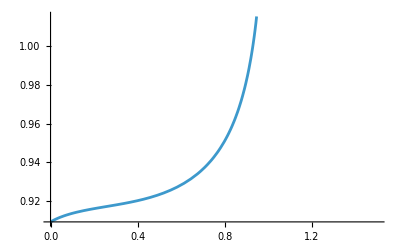

```mathematica
Plot[1+ αStr/Pi ω[s], {s, 0, 1.5}]
```

Вспомогательная функция h(m,s):

```mathematica
h[m_,s_] := -8/9 Log[m]+8/27+4/9(4 m^2)/s -2/9(2+(4 m^2)/s)Sqrt[Abs[1-(4 m^2)/s]] (Log[Abs[(Sqrt[1-(4 m^2)/s]+1)/(Sqrt[1-(4 m^2)/s]-1)]]-I Pi)/; (4 m^2)/s<=1 /; m!=0
h[m_,s_] := -8/9 Log[m]+8/27+4/9(4 m^2)/s -2/9(2+(4 m^2)/s)Sqrt[Abs[1-(4 m^2)/s]] 2 ArcTan[1/Sqrt[(4 m^2)/s - 1]]/; (4 m^2)/s>1 /; m!=0
h[m_,s_] :=8/27-4/9 Log[s] + 4/9 I Pi /; m==0
```

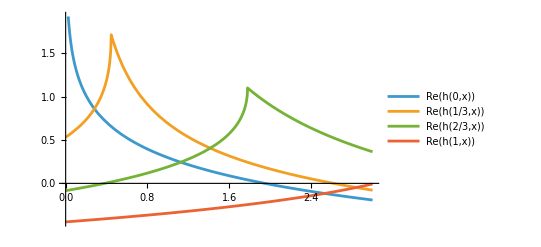

```mathematica
Plot[{Re[h[0,x]],  Re[h[1/3,x]], Re[h[2/3,x]], Re[h[1,x]]}, {x, 0, 3}, PlotLegends->"Expressions"]
```

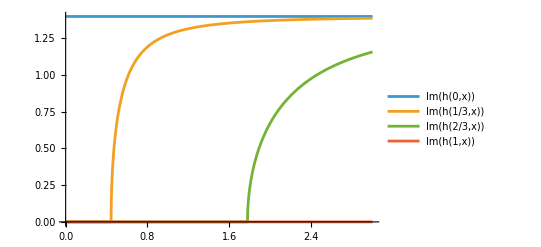

```mathematica
Plot[{Im[h[0,x]],  Im[h[1/3,x]], Im[h[2/3,x]], Im[h[1,x]]}, {x, 0, 3}, PlotLegends->"Expressions"]
```

Вспомогательная функция H(m_c,s):

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiEE)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2SEE)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770EE)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040EE)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160EE)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415EE)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="e"
```

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiMuMu)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2SMuMu)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770MuMu)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040MuMu)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160MuMu)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415MuMu)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="mu"
```

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiTauTau)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2STauTau)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770TauTau)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040TauTau)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160TauTau)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415TauTau)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="tau"
```

```mathematica
Plot[Abs[Hc[1/4.58, x, "mu"]], {x, 0, 1.9}, PlotLabels->"|H(m_c=0,s)|"]
```

-Graphics-

Вспомогательная функция H(m_u,s):

```mathematica
Hu[m_, s_, lep_] := h[m,s]-1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770EE)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782EE)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="e"
```

```mathematica
Hu[m_, s_, lep_] := h[m,s]- 1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770MuMu)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782MuMu)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="mu"
```

```mathematica
Hu[m_, s_, lep_] := h[m,s]- 1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770TauTau)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782TauTau)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="tau"
```

```mathematica
Plot[Abs[Hu[0.5, x, "mu"]], {x, 0.02, 0.05}, PlotLabels->"|H(m_u=0,s)|"]
```

-Graphics-

### 6) Вильсоновские коэффициенты:

Подразумевается  соглашение C_2(M_W) = -1. Масштабный фактор, на котором берутся значения коэффициентов: μ_0 = 5 ГэВ.

 Численные значения взяты из работ, указывавшихся в пунтке (5) данного раздела.

```mathematica
C1 = 0.241;
C2 = -1.1;
C3 = -0.0104;
C4 = 0.02433;
C5= - 0.00706;
C6 = 0.0294;
C7gamma = 0.312;
C9V = -4.21;
C10A = 4.41;
```

Эффективный коэффициент Вильсона (C_(9V))^eff(μ, s), учитывающий с-анти-с петли, а также вклад резонансов:

```mathematica
C9Veff[s_,Mbmeson_, lep_,supp_] = (1+αStr/Pi ω[s mb^2/Mbmeson^2])C9V - (3C1+C2)(λu[supp] Hu[mu/mb, s,lep] + λc[supp] Hc[(1.2mc)/mb, s,lep])+(3 C3 + C4+ 3 C5+ C6) (2/9 + Hc[(1.2mc)/mb, s,lep])- 1/2(4C3 + 4C4 + 3C5+ C6) h[1, s] - 1/2(C3+ 3C4)h[ms/mb,s];
```

```mathematica
LogPlot[Abs[C9Veff[s, MB, "tau", "ts"]], {s, 0, 1.8},  PlotLabels->"|(C_(9  V))^eff(s)|"]
```

-Graphics-

```mathematica
Plot[Im[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.2},  PlotLabels->"Im((C_(9  V))^eff(s))"]
```

-Graphics-

```mathematica
Plot[Re[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.2},  PlotLabels->"Re((C_(9  V))^eff(s))"]
```

-Graphics-

### 7) Форм-факторы:

Определение форм-факторов и их численные значения взяты из работы [Weak form factors for heavy meson decays: An update // D. Melikhov and B. Stech]

Константы f(0), σ_1, σ_2 для распада B_s^0-> K^(*0)l^+l^-
1) Для функции V(q^2):

```mathematica
VformBsK = 0.38;
dVformBsK = 1/2 0.11;
σV1BsK = 0.66;
σV2BsK = 0.30;
```

2) Для функции A_0(q^2):

```mathematica
A0formBsK = 0.37;
σA01BsK = 0.60;
σA02BsK = 0.16;
```

3) Для функции A_1(q^2):

```mathematica
A1formBsK = 0.29;
dA1formBsK =1/2 0.08;
σA11BsK = 0.86;
σA12BsK = 0.60;
```

4) Для функции A_2(q^2):

```mathematica
A2formBsK = 0.26;
dA2formBsK =1/2 0.09;
σA21BsK = 1.32;
σA22BsK = 0.54;
```

5) Для функции T_1(q^2):

```mathematica
T1formBsK = 0.32;
dT1formBsK = 1/2 0.10;
σT11BsK = 0.66;
σT12BsK = 0.31;
```

6) Для функции T_2(q^2):

```mathematica
T2formBsK = 0.32;
σT21BsK = 0.98;
σT22BsK = 0.90;
```

7) Для функции T_3(q^2):

```mathematica
T3formBsK = 0.23;
σT31BsK = 1.42;
σT32BsK = 0.62;
```

Константы M_P и M_V:

```mathematica
MPBsK = 5270;
```

```mathematica
MVBsK = 5320;
```

Константы f(0), σ_1, σ_2 для распада B^0-> K^(*0)l^+l^-
1) Для функции V(q^2):

```mathematica
VformBK = 0.39;
dVformBK =1/2 0.11;
σV1BK = 0.45;
σV2BK = 0.0;
```

2) Для функции A_0(q^2):

```mathematica
A0formBK = 0.27;
σA01BK = 0.46;
σA02BK = 0.;
```

3) Для функции A_1(q^2):

```mathematica
A1formBK = 0.28;
dA1formBK =1/2 0.08;
σA11BK = 0.64;
σA12BK = 0.36;
```

4) Для функции A_2(q^2):

```mathematica
A2formBK = 0.23;
dA2formBK =1/2 0.09;
σA21BK = 1.23;
σA22BK = 0.38;
```

5) Для функции T_1(q^2):

```mathematica
T1formBK = 0.14;
dT1formBK =1/2 0.10;
σT11BK = 0.45;
σT12BK = 0.;
```

6) Для функции T_2(q^2):

```mathematica
T2formBK = 0.23;
σT21BK = 0.72;
σT22BK = 0.62;
```

7) Для функции T_3(q^2):

```mathematica
T3formBK = 0.27;
σT31BK = 1.31;
σT32BK = 0.41;
```

Константы M_P и M_V:

```mathematica
MPBK = 5370;
```

```mathematica
MVBK = 5420;
```

Константы f(0), σ_1, σ_2 для распада B^0-> ρ^0 l^+l^-
1) Для функции V(q^2):

```mathematica
VformBrho = 0.31;
dVformBrho =1/2 0.14;
σV1Brho = 0.59;
σV2Brho = 0.0;
```

2) Для функции A_0(q^2):

```mathematica
A0formBrho = 0.30;
σA01Brho = 0.54;
σA02Brho = 0.;
```

3) Для функции A_1(q^2):

```mathematica
A1formBrho = 0.26;
dA1formBrho =1/2 0.10;
σA11Brho = 0.73;
σA12Brho = 0.10;
```

4) Для функции A_2(q^2):

```mathematica
A2formBrho = 0.24;
dA2formBrho =1/2 0.11;
σA21Brho = 1.40;
σA22Brho = 0.50;
```

5) Для функции T_1(q^2):

```mathematica
T1formBrho = 0.27;
dT1formBrho =1/2 0.12;
σT11Brho = 0.60;
σT12Brho = 0.;
```

6) Для функции T_2(q^2):

```mathematica
T2formBrho = 0.27;
σT21Brho = 0.74;
σT22Brho = 0.19;
```

7) Для функции T_3(q^2):

```mathematica
T3formBrho = 0.19;
σT31Brho = 1.42;
σT32Brho = 0.51;
```

Константы M_P и M_V:

```mathematica
MPBrho = 5270;
```

```mathematica
MVBrho = 5320;
```

Константы f(0), σ_1, σ_2 для распада B_s^0-> ϕ^0 l^+l^-
1) Для функции V(q^2):

```mathematica
VformBsphi = 0.44;
dVformBsphi =1/2 0.11;
σV1Bsphi = 0.62;
σV2Bsphi = 0.20;
```

2) Для функции A_0(q^2):

```mathematica
A0formBsphi = 0.42;
σA01Bsphi = 0.55;
σA02Bsphi = 0.12;
```

3) Для функции A_1(q^2):

```mathematica
A1formBsphi = 0.34;
dA1formBsphi =1/2 0.08;
σA11Bsphi = 0.73;
σA12Bsphi = 0.42;
```

4) Для функции A_2(q^2):

```mathematica
A2formBsphi = 0.31;
dA2formBsphi = 1/2 0.09;
σA21Bsphi = 1.30;
σA22Bsphi = 0.52;
```

5) Для функции T_1(q^2):

```mathematica
T1formBsphi = 0.38;
dT1formBsphi =1/2 0.10;
σT11Bsphi = 0.62;
σT12Bsphi = 0.20;
```

6) Для функции T_2(q^2):

```mathematica
T2formBsphi = 0.38;
σT21Bsphi = 0.83;
σT22Bsphi = 0.71;
```

7) Для функции T_3(q^2):

```mathematica
T3formBsphi = 0.26;
σT31Bsphi = 1.41;
σT32Bsphi = 0.57;
```

Константы M_P и M_V:

```mathematica
MPBsphi = 5370;
```

```mathematica
MVBsphi = 5420;
```

Определение функций V(q^2),A_0(q^2),A_1(q^2),A_2(q^2),T_1(q^2),T_2(q^2),T_3(q^2)

```mathematica
V[s_, type_] := VformBsK/((1-s (MBs/MVBsK)^2)(1-σV1BsK s (MBs/MVBsK)^2+σV2BsK s^2 (MBs/MVBsK)^4))/; type=="BsK"
V[s_, type_] := (VformBsK+ dVformBsK)/((1-s (MBs/MVBsK)^2)(1-σV1BsK s (MBs/MVBsK)^2+σV2BsK s^2 (MBs/MVBsK)^4))/; type=="BsK+"
V[s_, type_] := (VformBsK- dVformBsK)/((1-s (MBs/MVBsK)^2)(1-σV1BsK s (MBs/MVBsK)^2+σV2BsK s^2 (MBs/MVBsK)^4))/; type=="BsK-"

V[s_, type_] := VformBK/((1-s (MB/MVBK)^2)(1-σV1BK s (MB/MVBK)^2+σV2BK s^2 (MB/MVBK)^4))/; type=="BK"
V[s_, type_] := (VformBK+dVformBK)/((1-s (MB/MVBK)^2)(1-σV1BK s (MB/MVBK)^2+σV2BK s^2 (MB/MVBK)^4))/; type=="BK+"
V[s_, type_] := (VformBK-dVformBK)/((1-s (MB/MVBK)^2)(1-σV1BK s (MB/MVBK)^2+σV2BK s^2 (MB/MVBK)^4))/; type=="BK-"

V[s_, type_] := VformBrho/((1-s (MB/MVBrho)^2)(1-σV1Brho s (MB/MVBrho)^2+σV2Brho s^2 (MB/MVBrho)^4))/; type=="Brho"
V[s_, type_] := (VformBrho+dVformBrho)/((1-s (MB/MVBrho)^2)(1-σV1Brho s (MB/MVBrho)^2+σV2Brho s^2 (MB/MVBrho)^4))/; type=="Brho+"
V[s_, type_] := (VformBrho-dVformBrho)/((1-s (MB/MVBrho)^2)(1-σV1Brho s (MB/MVBrho)^2+σV2Brho s^2 (MB/MVBrho)^4))/; type=="Brho-"

V[s_, type_] := VformBsphi/((1-s (MBs/MVBsphi)^2)(1-σV1Bsphi s (MBs/MVBsphi)^2+σV2Bsphi s^2 (MBs/MVBsphi)^4))/; type=="Bsphi"
V[s_, type_] := (VformBsphi+dVformBsphi)/((1-s (MBs/MVBsphi)^2)(1-σV1Bsphi s (MBs/MVBsphi)^2+σV2Bsphi s^2 (MBs/MVBsphi)^4))/; type=="Bsphi+"
V[s_, type_] := (VformBsphi-dVformBsphi)/((1-s (MBs/MVBsphi)^2)(1-σV1Bsphi s (MBs/MVBsphi)^2+σV2Bsphi s^2 (MBs/MVBsphi)^4))/; type=="Bsphi-"

A0[s_, type_] := A0formBsK/((1-s (MBs/MPBsK)^2)(1-σA01BsK s (MBs/MPBsK)^2+σA02BsK s^2(MBs/MPBsK)^4))/; type=="BsK"
A0[s_, type_] := A0formBsK/((1-s (MBs/MPBsK)^2)(1-σA01BsK s (MBs/MPBsK)^2+σA02BsK s^2(MBs/MPBsK)^4))/; type=="BsK+"
A0[s_, type_] := A0formBsK/((1-s (MBs/MPBsK)^2)(1-σA01BsK s (MBs/MPBsK)^2+σA02BsK s^2(MBs/MPBsK)^4))/; type=="BsK-"
A0[s_, type_] := A0formBK/((1-s (MB/MPBK)^2)(1-σA01BK s (MB/MPBK)^2+σA02BK s^2(MB/MPBK)^4))/; type=="BK"
A0[s_, type_] := A0formBK/((1-s (MB/MPBK)^2)(1-σA01BK s (MB/MPBK)^2+σA02BK s^2(MB/MPBK)^4))/; type=="BK+"
A0[s_, type_] := A0formBK/((1-s (MB/MPBK)^2)(1-σA01BK s (MB/MPBK)^2+σA02BK s^2(MB/MPBK)^4))/; type=="BK-"
A0[s_, type_] := A0formBrho/((1-s (MB/MPBrho)^2)(1-σA01Brho s (MB/MPBrho)^2+σA02Brho s^2(MB/MPBrho)^4))/; type=="Brho"
A0[s_, type_] := A0formBrho/((1-s (MB/MPBrho)^2)(1-σA01Brho s (MB/MPBrho)^2+σA02Brho s^2(MB/MPBrho)^4))/; type=="Brho+"
A0[s_, type_] := A0formBrho/((1-s (MB/MPBrho)^2)(1-σA01Brho s (MB/MPBrho)^2+σA02Brho s^2(MB/MPBrho)^4))/; type=="Brho-"
A0[s_, type_] := A0formBsphi/((1-s (MBs/MPBsphi)^2)(1-σA01Bsphi s (MBs/MPBsphi)^2+σA02Bsphi s^2(MBs/MPBsphi)^4))/; type=="Bsphi"
A0[s_, type_] := A0formBsphi/((1-s (MBs/MPBsphi)^2)(1-σA01Bsphi s (MBs/MPBsphi)^2+σA02Bsphi s^2(MBs/MPBsphi)^4))/; type=="Bsphi+"
A0[s_, type_] := A0formBsphi/((1-s (MBs/MPBsphi)^2)(1-σA01Bsphi s (MBs/MPBsphi)^2+σA02Bsphi s^2(MBs/MPBsphi)^4))/; type=="Bsphi-"


A1[s_, type_] := A1formBsK/(1-σA11BsK s(MBs/MVBsK)^2+σA12BsK s^2 (MBs/MVBsK)^4)/; type=="BsK"
A1[s_, type_] := (A1formBsK+dA1formBsK)/(1-σA11BsK s(MBs/MVBsK)^2+σA12BsK s^2 (MBs/MVBsK)^4)/; type=="BsK+"
A1[s_, type_] := (A1formBsK-dA1formBsK)/(1-σA11BsK s(MBs/MVBsK)^2+σA12BsK s^2 (MBs/MVBsK)^4)/; type=="BsK-"

A1[s_, type_] := A1formBK/(1-σA11BK s(MB/MVBK)^2+σA12BK s^2 (MB/MVBK)^4)/; type=="BK"
A1[s_, type_] := (A1formBK + dA1formBK)/(1-σA11BK s(MB/MVBK)^2+σA12BK s^2 (MB/MVBK)^4)/; type=="BK+"
A1[s_, type_] := (A1formBK - dA1formBK)/(1-σA11BK s(MB/MVBK)^2+σA12BK s^2 (MB/MVBK)^4)/; type=="BK-"

A1[s_, type_] := A1formBsphi/(1-σA11Bsphi s(MBs/MVBsphi)^2+σA12Bsphi s^2 (MBs/MVBsphi)^4)/; type=="Bsphi"
A1[s_, type_] := (A1formBsphi+ dA1formBsphi)/(1-σA11Bsphi s(MBs/MVBsphi)^2+σA12Bsphi s^2 (MBs/MVBsphi)^4)/; type=="Bsphi+"
A1[s_, type_] := (A1formBsphi- dA1formBsphi)/(1-σA11BK s(MB/MVBK)^2+σA12BK s^2 (MB/MVBK)^4)/; type=="Bsphi-"

A1[s_, type_] := A1formBrho/(1-σA11Brho s(MB/MVBrho)^2+σA12Brho s^2 (MB/MVBrho)^4)/; type=="Brho"
A1[s_, type_] := (A1formBrho + dA1formBrho)/(1-σA11Brho s(MB/MVBrho)^2+σA12Brho s^2 (MB/MVBrho)^4)/; type=="Brho+"
A1[s_, type_] := (A1formBrho - dA1formBrho)/(1-σA11Brho s(MB/MVBrho)^2+σA12Brho s^2 (MB/MVBrho)^4)/; type=="Brho-"


A2[s_, type_] := A2formBsK/(1-σA21BsK s(MBs/MVBsK)^2+σA22BsK s^2 (MBs/MVBsK)^4)/; type=="BsK"
A2[s_, type_] := (A2formBsK+dA2formBsK)/(1-σA21BsK s(MBs/MVBsK)^2+σA22BsK s^2 (MBs/MVBsK)^4)/; type=="BsK+"
A2[s_, type_] := (A2formBsK-dA2formBsK)/(1-σA21BsK s(MBs/MVBsK)^2+σA22BsK s^2 (MBs/MVBsK)^4)/; type=="BsK-"

A2[s_, type_] := A2formBK/(1-σA21BK s(MB/MVBK)^2+σA22BK s^2 (MB/MVBK)^4)/; type=="BK"
A2[s_, type_] := (A2formBK + dA2formBK)/(1-σA21BK s(MB/MVBK)^2+σA22BK s^2 (MB/MVBK)^4)/; type=="BK+"
A2[s_, type_] := (A2formBK - dA2formBK)/(1-σA21BK s(MB/MVBK)^2+σA22BK s^2 (MB/MVBK)^4)/; type=="BK-"

A2[s_, type_] := A2formBsphi/(1-σA21Bsphi s(MBs/MVBsphi)^2+σA22Bsphi s^2 (MBs/MVBsphi)^4)/; type=="Bsphi"
A2[s_, type_] := (A2formBsphi+ dA2formBsphi)/(1-σA21Bsphi s(MBs/MVBsphi)^2+σA22Bsphi s^2 (MBs/MVBsphi)^4)/; type=="Bsphi+"
A2[s_, type_] := (A2formBsphi- dA2formBsphi)/(1-σA21BK s(MB/MVBK)^2+σA22BK s^2 (MB/MVBK)^4)/; type=="Bsphi-"

A2[s_, type_] := A2formBrho/(1-σA21Brho s(MB/MVBrho)^2+σA22Brho s^2 (MB/MVBrho)^4)/; type=="Brho"
A2[s_, type_] := (A2formBrho + dA2formBrho)/(1-σA21Brho s(MB/MVBrho)^2+σA22Brho s^2 (MB/MVBrho)^4)/; type=="Brho+"
A2[s_, type_] := (A2formBrho - dA2formBrho)/(1-σA21Brho s(MB/MVBrho)^2+σA22Brho s^2 (MB/MVBrho)^4)/; type=="Brho-"


T1[s_, type_] := T1formBsK/((1-s (MBs/MVBsK)^2)(1-σT11BsK s(MBs/MVBsK)^2+σT12BsK s^2 (MBs/MVBsK)^4))/; type=="BsK"
T1[s_, type_] := (T1formBsK+dT1formBsK)/((1-s (MBs/MVBsK)^2)(1-σT11BsK s(MBs/MVBsK)^2+σT12BsK s^2 (MBs/MVBsK)^4))/; type=="BsK+"
T1[s_, type_] := (T1formBsK-dT1formBsK)/((1-s (MBs/MVBsK)^2)(1-σT11BsK s(MBs/MVBsK)^2+σT12BsK s^2 (MBs/MVBsK)^4))/; type=="BsK-"

T1[s_, type_] := T1formBK/((1-s (MB/MVBK)^2)(1-σT11BK s(MB/MVBK)^2+σT12BK s^2 (MB/MVBK)^4))/; type=="BK"
T1[s_, type_] := (T1formBK + dT1formBK)/((1-s (MB/MVBK)^2)(1-σT11BK s(MB/MVBK)^2+σT12BK s^2 (MB/MVBK)^4))/; type=="BK+"
T1[s_, type_] := (T1formBK - dT1formBK)/((1-s (MB/MVBK)^2)(1-σT11BK s(MB/MVBK)^2+σT12BK s^2 (MB/MVBK)^4))/; type=="BK-"

T1[s_, type_] := T1formBsphi/((1-s (MBs/MVBsphi)^2)(1-σT11Bsphi s(MBs/MVBsphi)^2+σT12Bsphi s^2 (MBs/MVBsphi)^4))/; type=="Bsphi"
T1[s_, type_] := (T1formBsphi+ dT1formBsphi)/((1-s (MBs/MVBsphi)^2)(1-σT11Bsphi s(MBs/MVBsphi)^2+σT12Bsphi s^2 (MBs/MVBsphi)^4))/; type=="Bsphi+"
T1[s_, type_] := (T1formBsphi- dT1formBsphi)/((1-s (MBs/MVBsphi)^2)(1-σT11Bsphi s(MBs/MVBsphi)^2+σT12Bsphi s^2 (MBs/MVBsphi)^4))/; type=="Bsphi-"

T1[s_, type_] := T1formBrho/((1-s (MB/MVBrho)^2)(1-σT11Brho s(MB/MVBrho)^2+σT12Brho s^2 (MB/MVBrho)^4))/; type=="Brho"
T1[s_, type_] := (T1formBrho + dT1formBrho)/((1-s (MB/MVBrho)^2)(1-σT11Brho s(MB/MVBrho)^2+σT12Brho s^2 (MB/MVBrho)^4))/; type=="Brho+"
T1[s_, type_] := (T1formBrho - dT1formBrho)/((1-s (MB/MVBrho)^2)(1-σT11Brho s(MB/MVBrho)^2+σT12Brho s^2 (MB/MVBrho)^4))/; type=="Brho-"

T2[s_, type_] := T2formBsK/(1-σT21BsK s (MBs/MVBsK)^2+σT22BsK s^2(MBs/MVBsK)^4)/; type=="BsK"
T2[s_, type_] := T2formBsK/(1-σT21BsK s (MBs/MVBsK)^2+σT22BsK s^2(MBs/MVBsK)^4)/; type=="BsK+"
T2[s_, type_] := T2formBsK/(1-σT21BsK s (MBs/MVBsK)^2+σT22BsK s^2(MBs/MVBsK)^4)/; type=="BsK-"
T2[s_, type_] := T2formBK/(1-σT21BK s (MB/MVBK)^2+σT22BK s^2(MB/MVBK)^4)/; type=="BK"
T2[s_, type_] := T2formBK/(1-σT21BK s (MB/MVBK)^2+σT22BK s^2(MB/MVBK)^4)/; type=="BK+"
T2[s_, type_] := T2formBK/(1-σT21BK s (MB/MVBK)^2+σT22BK s^2(MB/MVBK)^4)/; type=="BK-"
T2[s_, type_] := T2formBrho/(1-σT21Brho s (MB/MVBrho)^2+σT22Brho s^2(MB/MVBrho)^4)/; type=="Brho"
T2[s_, type_] := T2formBrho/(1-σT21Brho s (MB/MVBrho)^2+σT22Brho s^2(MB/MVBrho)^4)/; type=="Brho+"
T2[s_, type_] := T2formBrho/(1-σT21Brho s (MB/MVBrho)^2+σT22Brho s^2(MB/MVBrho)^4)/; type=="Brho-"
T2[s_, type_] := T2formBsphi/(1-σT21Bsphi s (MBs/MVBsphi)^2+σT22Bsphi s^2(MBs/MVBsphi)^4)/; type=="Bsphi"
T2[s_, type_] := T2formBsphi/(1-σT21Bsphi s (MBs/MVBsphi)^2+σT22Bsphi s^2(MBs/MVBsphi)^4)/; type=="Bsphi+"
T2[s_, type_] := T2formBsphi/(1-σT21Bsphi s (MBs/MVBsphi)^2+σT22Bsphi s^2(MBs/MVBsphi)^4)/; type=="Bsphi-"

T3[s_, type_] := T3formBsK/(1-σT31BsK s (MBs/MVBsK)^2+σT32BsK s^2(MBs/MVBsK)^4)/; type=="BsK"
T3[s_, type_] := T3formBsK/(1-σT31BsK s (MBs/MVBsK)^2+σT32BsK s^2(MBs/MVBsK)^4)/; type=="BsK+"
T3[s_, type_] := T3formBsK/(1-σT31BsK s (MBs/MVBsK)^2+σT32BsK s^2(MBs/MVBsK)^4)/; type=="BsK-"
T3[s_, type_] := T3formBK/(1-σT31BK s (MB/MVBK)^2+σT32BK s^2(MB/MVBK)^4)/; type=="BK"
T3[s_, type_] := T3formBK/(1-σT31BK s (MB/MVBK)^2+σT32BK s^2(MB/MVBK)^4)/; type=="BK+"
T3[s_, type_] := T3formBK/(1-σT31BK s (MB/MVBK)^2+σT32BK s^2(MB/MVBK)^4)/; type=="BK-"
T3[s_, type_] := T3formBrho/(1-σT31Brho s (MB/MVBrho)^2+σT32Brho s^2(MB/MVBrho)^4)/; type=="Brho"
T3[s_, type_] := T3formBrho/(1-σT31Brho s (MB/MVBrho)^2+σT32Brho s^2(MB/MVBrho)^4)/; type=="Brho+"
T3[s_, type_] := T3formBrho/(1-σT31Brho s (MB/MVBrho)^2+σT32Brho s^2(MB/MVBrho)^4)/; type=="Brho-"
T3[s_, type_] := T3formBsphi/(1-σT31Bsphi s (MBs/MVBsphi)^2+σT32Bsphi s^2(MBs/MVBsphi)^4)/; type=="Bsphi"
T3[s_, type_] := T3formBsphi/(1-σT31Bsphi s (MBs/MVBsphi)^2+σT32Bsphi s^2(MBs/MVBsphi)^4)/; type=="Bsphi+"
T3[s_, type_] := T3formBsphi/(1-σT31Bsphi s (MBs/MVBsphi)^2+σT32Bsphi s^2(MBs/MVBsphi)^4)/; type=="Bsphi-"
```

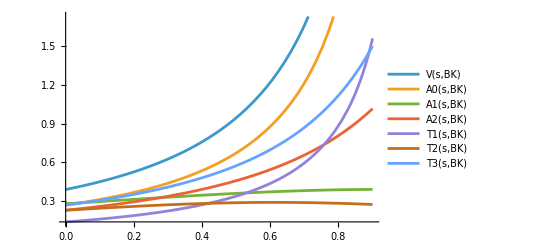

```mathematica
Plot[{V[s,"BK"],A0[s,"BK"],A1[s,"BK"],A2[s,"BK"],T1[s,"BK"],T2[s,"BK"],T3[s,"BK"]}, {s, 0, 0.9},PlotLegends->"Expressions"]
```

Определение функций g(q^2), g_0(q^2), g_+(q^2), g_-(q^2), a_+(q^2), a_-(q^2), f(q^2):

```mathematica
g[s_ ,type_,Mbmeson_, Mkaon_] = V[s,type]/(Mbmeson+Mkaon);
gplus[s_,type_] = -2T1[s,type];
gminus[s_,type_,Mbmeson_, Mkaon_] =- (Mbmeson^2-Mkaon^2)/(s Mbmeson^2)(2T2[s,type]+gplus[s,type]);
g0[s_,type_,Mbmeson_, Mkaon_] = 2/(Mbmeson^2-Mkaon^2)gminus[s,type,Mbmeson, Mkaon]-(4T3[s,type])/(Mbmeson+Mkaon)^2;
f[s_,type_,Mbmeson_, Mkaon_] = (Mbmeson+Mkaon)A1[s,type];
aplus[s_,type_,Mbmeson_, Mkaon_] = (-A2[s,type])/(Mbmeson+Mkaon);
aminus[s_,type_,Mbmeson_, Mkaon_] = 1/(s Mbmeson^2)(2Mkaon A0[s,type]-f[s,type,Mbmeson, Mkaon]-(Mbmeson^2-Mkaon^2)aplus[s,type,Mbmeson, Mkaon]);
```

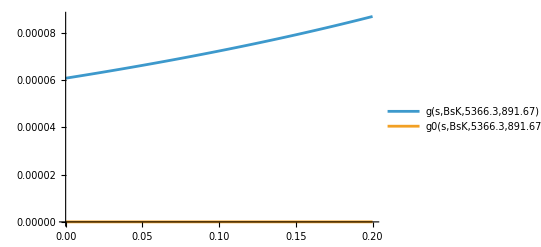

```mathematica
Plot[{g[s, "BsK", MBs, Mk],g0[s, "BsK", MBs, Mk]}, {s, -0., 0.2},PlotLegends->"Expressions"]
```

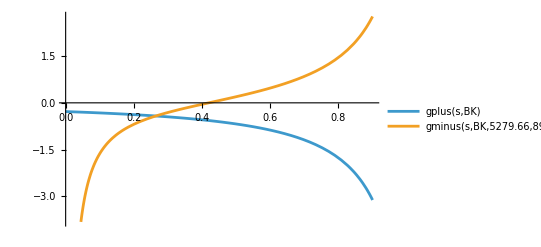

```mathematica
Plot[{gplus[s, "BK"],gminus[s, "BK", MB, Mk]}, {s, 0, 0.9},PlotLegends->"Expressions"]
```

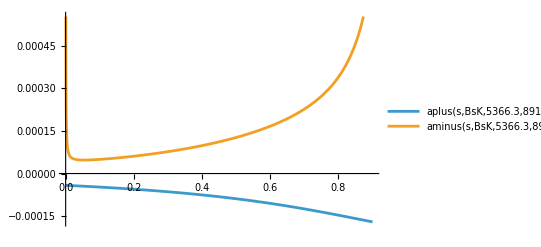

```mathematica
Plot[{aplus[s, "BsK", MBs, Mk],aminus[s, "BsK", MBs, Mk]}, {s, 0, 0.9},PlotLegends->"Expressions"]
```

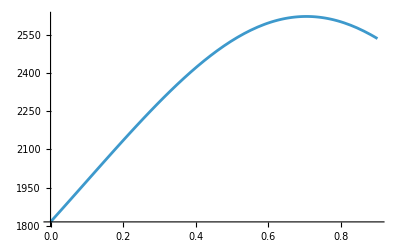

```mathematica
Plot[f[s, "BsK", MBs, Mk], {s, 0, 0.9},PlotLegends->"f[s]"]
```

## Часть 2. Дифференциальная ширина, branching ratio.

### 1) Вспомогательные функции B_0(q^2), B_+(q^2), H_+(q^2), R(q^2), R_1(q^2), F(q^2), G(q^2), а также ϕ(s,r), β_V(s), (β^(1))_V(s), (β^(2))_V(s), δ_V и Π(s,t), t(cosθ)

```mathematica
B0[s_,type_,Mbmeson_, Mkaon_] = gplus[s,type]+gminus[s,type,Mbmeson, Mkaon] s/(1-rhat[Mkaon,Mbmeson]);


Bplus[s_,type_,Mbmeson_, Mkaon_] = -s Mbmeson^2 g0[s,type,Mbmeson, Mkaon]/2-gplus[s,type];


HplusSquared[s_,type_,Mbmeson_, Mkaon_, lep_,supp_] = Abs[C9Veff[s Mbmeson^2/mb^2,Mbmeson, lep,supp]Mbmeson aplus[s,type,Mbmeson, Mkaon]- (2 C7gamma)/s mb/Mbmeson Bplus[s,type,Mbmeson, Mkaon]]^2 + Abs[C10A Mbmeson aplus[s,type,Mbmeson, Mkaon]]^2;


R[s_,type_,Mbmeson_, Mkaon_, lep_,supp_] = Re[(C9Veff[s Mbmeson^2/mb^2,Mbmeson, lep,supp] f[s,type,Mbmeson, Mkaon]/Mbmeson- 2 C7gamma/s mb/Mbmeson(1-rhat[Mkaon,Mbmeson])B0[s,type,Mbmeson, Mkaon])Conjugate[(C9Veff[s Mbmeson^2/mb^2,Mbmeson, lep,supp]Mbmeson aplus[s,type,Mbmeson, Mkaon]- (2 C7gamma)/s mb/Mbmeson Bplus[s,type,Mbmeson, Mkaon])]] + Abs[C10A]^2 Re[aplus[s,type,Mbmeson, Mkaon]Conjugate[f[s,type,Mbmeson, Mkaon]]];

R1[s_,type_,Mbmeson_, Mkaon_, lep_,supp_] = Re[(C9Veff[s Mbmeson^2/mb^2,Mbmeson, lep,supp]Mbmeson g[s,type,Mbmeson, Mkaon]- 2 C7gamma/s mb/Mbmeson gplus[s,type])(C10A f[s,type,Mbmeson, Mkaon]/Mbmeson)*] + Re[(C9Veff[s Mbmeson^2/mb^2,Mbmeson, lep,supp] f[s,type,Mbmeson, Mkaon]/Mbmeson- 2 C7gamma/s mb/Mbmeson(1-rhat[Mkaon,Mbmeson])B0[s,type,Mbmeson, Mkaon])(C10A Mbmeson g[s,type,Mbmeson, Mkaon])*];


FSquared[s_,type_,Mbmeson_, Mkaon_, lep_,supp_] = Abs[C9Veff[s Mbmeson^2/mb^2,Mbmeson, lep,supp] f[s,type,Mbmeson, Mkaon]/Mbmeson- 2 C7gamma/s mb/Mbmeson(1-rhat[Mkaon,Mbmeson])B0[s,type,Mbmeson, Mkaon]]^2+Abs[C10A f[s,type,Mbmeson, Mkaon]/Mbmeson]^2;
GSquared[s_,type_,Mbmeson_, Mkaon_, lep_,supp_] = Abs[C9Veff[s Mbmeson^2/mb^2,Mbmeson, lep,supp]Mbmeson g[s,type,Mbmeson, Mkaon]- (2 C7gamma)/s mb/Mbmeson gplus[s,type]]^2+ Abs[C10A Mbmeson g[s,type,Mbmeson, Mkaon]]^2;
```

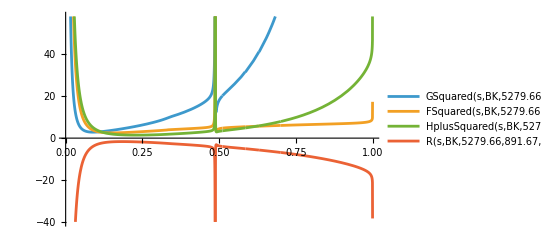

```mathematica
Plot[{GSquared[s,"BK",MB, Mk, "tau","ts"], FSquared[s,"BK",MB, Mk, "tau","ts"], HplusSquared[s,"BK",MB, Mk, "tau","ts"], R[s,"BK",MB, Mk, "tau","ts"]}, {s, 0, 1}, PlotLegends->"Expressions"]
```

```mathematica
ϕ[s_,Mbmeson_, Mkaon_] = 1 + rhat[Mkaon,Mbmeson]^2+s^2-2rhat[Mkaon,Mbmeson]-2s-2rhat[Mkaon,Mbmeson] s;
δV[s_,type_,Mbmeson_, Mkaon_,Mlepton_] = Abs[C10A]^2/2 ϕ[s,Mbmeson, Mkaon](-2 Abs[g[s,type,Mbmeson, Mkaon]Mbmeson]^2- 3/ϕ[s,Mbmeson, Mkaon] Abs[f[s,type,Mbmeson, Mkaon]/Mbmeson]^2+ (2(1+mhat[Mlepton,Mbmeson])-s)/(4 rhat[Mkaon,Mbmeson])Abs[aplus[s,type,Mbmeson, Mkaon]Mbmeson]^2+ s/(4rhat[Mkaon,Mbmeson])Abs[aminus[s,type,Mbmeson, Mkaon]Mbmeson]^2+1/(2 rhat[Mkaon,Mbmeson])Re[f[s,type,Mbmeson, Mkaon]Conjugate[aplus[s,type,Mbmeson, Mkaon]]+ f[s,type,Mbmeson, Mkaon]Conjugate[aminus[s,type,Mbmeson, Mkaon]]] +(1-rhat[Mkaon,Mbmeson])/(2rhat[Mkaon,Mbmeson])Re[Mbmeson aplus[s,type,Mbmeson, Mkaon]Mbmeson aminus[s,type,Mbmeson, Mkaon]]);
βV[s_,type_,Mbmeson_, Mkaon_, lep_,supp_] = 2 ϕ[s,Mbmeson, Mkaon] s GSquared[s,type,Mbmeson, Mkaon, lep,supp] + (2s + (1-rhat[Mkaon,Mbmeson]-s)^2/(4 rhat[Mkaon,Mbmeson]))FSquared[s,type,Mbmeson, Mkaon, lep,supp] + ϕ[s,Mbmeson, Mkaon]^2/(4 rhat[Mkaon,Mbmeson])HplusSquared[s,type,Mbmeson, Mkaon, lep,supp] - ϕ[s,Mbmeson, Mkaon]/(2 rhat[Mkaon,Mbmeson])(s -1+rhat[Mkaon,Mbmeson])R[s,type,Mbmeson, Mkaon, lep,supp];
```

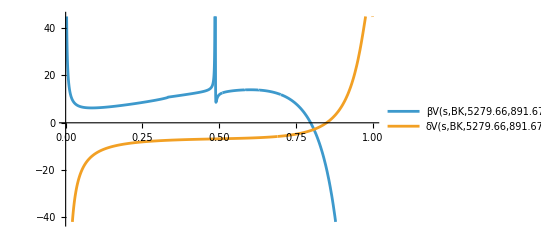

```mathematica
Plot[{βV[s,"BK",MB, Mk, "tau","ts"], δV[s,"BK",MB, Mk, mtau]}, {s, 0, 1}, PlotLegends->"Expressions"]
```

```mathematica
tMand[s_,cos_,Mbmeson_, Mkaon_,Mlepton_] = 1/2(1+rhat[Mkaon,Mbmeson]+2 mhat[Mlepton,Mbmeson] - s+Sqrt[ 1-4 mhat[Mlepton,Mbmeson]/s]Sqrt[ϕ[s,Mbmeson, Mkaon]]cos);
Π[s_,cos_,Mbmeson_, Mkaon_,Mlepton_] = (tMand[s,cos,Mbmeson, Mkaon,Mlepton]-1)(tMand[s,cos,Mbmeson, Mkaon,Mlepton]-rhat[Mkaon,Mbmeson])+s tMand[s,cos,Mbmeson, Mkaon,Mlepton] + mhat[Mlepton,Mbmeson](1+rhat[Mkaon,Mbmeson] +mhat[Mlepton,Mbmeson] - s - 2tMand[s,cos,Mbmeson, Mkaon,Mlepton]);

βV1[s_,cos_,type_,Mbmeson_, Mkaon_,Mlepton_, lep_,supp_] = ((s +2 mhat[Mlepton,Mbmeson])ϕ[s,Mbmeson, Mkaon]  +2s Π[s,cos,Mbmeson, Mkaon,Mlepton])GSquared[s,type,Mbmeson, Mkaon, lep,supp]+(s+2mhat[Mlepton,Mbmeson]-Π[s,cos,Mbmeson, Mkaon,Mlepton]/(2 rhat[Mkaon,Mbmeson]))FSquared[s,type,Mbmeson, Mkaon, lep,supp] -ϕ[s,Mbmeson, Mkaon]/(2 rhat[Mkaon,Mbmeson])Π[s,cos,Mbmeson, Mkaon,Mlepton]HplusSquared[s,type,Mbmeson, Mkaon, lep,supp] + (s - 1 +rhat[Mkaon,Mbmeson])/rhat[Mkaon,Mbmeson] Π[s,cos,Mbmeson, Mkaon,Mlepton]R[s,type,Mbmeson, Mkaon, lep,supp];

βV2[s_,cos_,type_,Mbmeson_, Mkaon_,Mlepton_, lep_,supp_] = 2s(2 tMand[s,cos,Mbmeson, Mkaon,Mlepton] + s - rhat[Mkaon,Mbmeson] - 1 - 2mhat[Mlepton,Mbmeson])R1[s,type,Mbmeson, Mkaon, lep,supp];
```

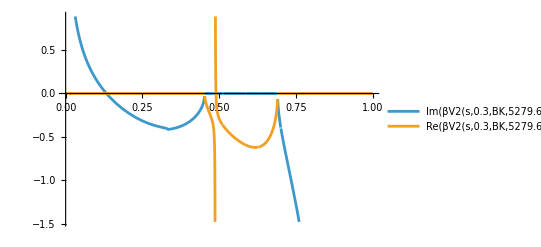

```mathematica
Plot[{Im[βV2[s,0.3,"BK",MB, Mk,mtau, "tau","ts"]], Re[βV2[s,0.3,"BK",MB, Mk, mtau,"tau","ts"]]}, {s, 0, 1}, PlotLegends->"Expressions"]
```

### 2) Дифференциальная ширина, определение функций.

```mathematica
dBrFreeExtended[s_,type_,Mbmeson_, Mkaon_,Mlepton_, lep_,supp_, Γfulll_] := (Gfermi^2 Mbmeson^5 Abs[Vts*Vtb]^2 α^2)/(Γfulll 1536 Pi^5)Sqrt[1 - (4 mhat[Mlepton, Mbmeson])/s]Sqrt[ϕ[s,Mbmeson, Mkaon]]((1+(2 mhat[Mlepton, Mbmeson])/s)βV[s,type,Mbmeson, Mkaon, lep,supp] + 12 mhat[Mlepton, Mbmeson] δV[s,type,Mbmeson, Mkaon,Mlepton])/; supp=="ts"
dBrFreeExtended[s_,type_,Mbmeson_, Mkaon_,Mlepton_, lep_,supp_, Γfulll_] := (Gfermi^2 Mbmeson^5 Abs[Vtd*Vtb]^2 α^2)/(Γfulll 1536 Pi^5)Sqrt[1 - (4mhat[Mlepton, Mbmeson])/s]Sqrt[ϕ[s,Mbmeson, Mkaon]]((1+(2 mhat[Mlepton, Mbmeson])/s)βV[s,type,Mbmeson, Mkaon, lep,supp] + 12 mhat[Mlepton, Mbmeson] δV[s,type,Mbmeson, Mkaon,Mlepton])/; supp=="td"
```

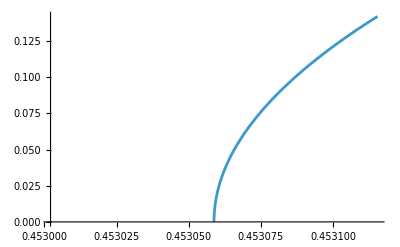

```mathematica
Plot[10^7 dBrFreeExtended[s,"BK",MB, Mk,mtau, "tau","ts", Γfull], {s, 3.9995 mhat[mtau, MB], 4.0005 mhat[mtau, MB]}]
```

```mathematica
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK",MB, Mk,me, "e","ts", Γfull]/; decay=="BKee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK+",MB, Mk,me, "e","ts", Γfull]/; decay=="BKee"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK-",MB, Mk,me, "e","ts", Γfull]/; decay=="BKee"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK",MB, Mk,mmu, "mu","ts", Γfull]/; decay=="BKmumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK+",MB, Mk,mmu, "mu","ts", Γfull]/; decay=="BKmumu"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK-",MB, Mk,mmu, "mu","ts", Γfull]/; decay=="BKmumu"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK",MB, Mk,mtau, "tau","ts", Γfull]/; decay=="BKtautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK+",MB, Mk,mtau, "tau","ts", Γfull]/; decay=="BKtautau"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BK-",MB, Mk,mtau, "tau","ts", Γfull]/; decay=="BKtautau"/; boundary == "-"



dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK",MBs, Mk,me, "e","td", ΓfullBs]/; decay=="BsKee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK+",MBs, Mk,me, "e","td", ΓfullBs]/; decay=="BsKee"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK-",MBs, Mk,me, "e","td", ΓfullBs]/; decay=="BsKee"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK",MBs, Mk,mmu, "mu","td", ΓfullBs]/; decay=="BsKmumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK+",MBs, Mk,mmu, "mu","td", ΓfullBs]/; decay=="BsKmumu"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK-",MBs, Mk,mmu, "mu","td", ΓfullBs]/; decay=="BsKmumu"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK",MBs, Mk,mtau, "tau","td", ΓfullBs]/; decay=="BsKtautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK+",MBs, Mk,mtau, "tau","td", ΓfullBs]/; decay=="BsKtautau"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"BsK-",MBs, Mk,mtau, "tau","td", ΓfullBs]/; decay=="BsKtautau"/; boundary == "-"



dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho",MB, Mrho,me, "e","ts", Γfull]/; decay=="Brhoee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho+",MB, Mrho,me, "e","ts", Γfull]/; decay=="Brhoee"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho-",MB, Mrho,me, "e","ts", Γfull]/; decay=="Brhoee"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho",MB, Mrho,mmu, "mu","ts", Γfull]/; decay=="Brhomumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho+",MB, Mrho,mmu, "mu","ts", Γfull]/; decay=="Brhomumu"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho-",MB, Mrho,mmu, "mu","ts", Γfull]/; decay=="Brhomumu"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho",MB, Mrho,mtau, "tau","ts", Γfull]/; decay=="Brhotautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho+",MB, Mrho,mtau, "tau","ts", Γfull]/; decay=="Brhotautau"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Brho-",MB, Mrho,mtau, "tau","ts", Γfull]/; decay=="Brhotautau"/; boundary == "-"


dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi",MBs, Mphi,me, "e","ts", ΓfullBs]/; decay=="Bsphiee"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi+",MBs, Mphi,me, "e","ts", ΓfullBs]/; decay=="Bsphiee"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi-",MBs, Mphi,me, "e","ts", ΓfullBs]/; decay=="Bsphiee"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi",MBs, Mphi,mmu, "mu","ts", ΓfullBs]/; decay=="Bsphimumu"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi+",MBs, Mphi,mmu, "mu","ts", ΓfullBs]/; decay=="Bsphimumu"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi-",MBs, Mphi,mmu, "mu","ts", ΓfullBs]/; decay=="Bsphimumu"/; boundary == "-"

dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi",MBs, Mphi,mtau, "tau","ts", ΓfullBs]/; decay=="Bsphitautau"/; boundary == ""
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi+",MBs, Mphi,mtau, "tau","ts", ΓfullBs]/; decay=="Bsphitautau"/; boundary == "+"
dBrFree[s_, decay_, boundary_] := dBrFreeExtended[s,"Bsphi-",MBs, Mphi,mtau, "tau","ts", ΓfullBs]/; decay=="Bsphitautau"/; boundary == "-"
```

```mathematica
V[mRatio_] :=Sqrt[1 - 4 mRatio ] ;
```

```mathematica
Vrel[mRatio_] := V[mRatio]/(1 - 2 mRatio);
```

```mathematica
CAS[v_] := Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/v]/Gamma[Sqrt[1-4 α^2]+1]]^2 Exp[Pi α/v];
Furry[v_] := Exp[Pi α/v];
```

```mathematica
Mbm[decay_]:=MB /;MemberQ[{"BKee","BKmumu","BKtautau","Brhoee", "Brhomumu", "Brhotautau"},decay]
Mbm[decay_]:=MBs /;MemberQ[{"BsKee","BsKmumu","BsKtautau", "Bsphiee","Bsphimumu","Bsphitautau"},decay]

Mlep[decay_]:=me /;MemberQ[{"BKee", "BsKee", "Brhoee", "Bsphiee"},decay]
Mlep[decay_]:=mmu /;MemberQ[{"BKmumu", "BsKmumu", "Brhomumu", "Bsphimumu"},decay]
Mlep[decay_]:=mtau /;MemberQ[{"BKtautau", "Brhotautau", "BsKtautau", "Bsphitautau"},decay]
```

```mathematica
dΓBrCoulomb [s_, decay_, boundary_] := dBrFree [s, decay, boundary]CAS[Vrel[mhat[Mlep[decay],Mbm[decay]]/s]]/;MemberQ[{"BsKee", "Bsphiee"},decay]
dΓBrCoulomb [s_, decay_, boundary_] := dBrFree [s, decay, boundary] CAS[Vrel[mhat[Mlep[decay],Mbm[decay]]/s]]/;MemberQ[{"BsKmumu", "Bsphimumu"},decay]
dΓBrCoulomb [s_, decay_, boundary_] := dBrFree [s, decay, boundary] CAS[Vrel[mhat[Mlep[decay],Mbm[decay]]/s]]/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dΓBrCoulomb [s_, decay_, boundary_] := dBrFree [s, decay, boundary]CAS[Vrel[mhat[Mlep[decay],Mbm[decay]]/s]]/;MemberQ[{"BKee", "Brhoee"},decay]
dΓBrCoulomb [s_, decay_, boundary_] := dBrFree [s, decay, boundary]CAS[Vrel[mhat[Mlep[decay],Mbm[decay]]/s]]/;MemberQ[{"BKmumu", "Brhomumu"},decay]
dΓBrCoulomb [s_, decay_, boundary_] := dBrFree [s, decay, boundary] CAS[Vrel[mhat[Mlep[decay],Mbm[decay]]/s]]/;MemberQ[{"BKtautau", "Brhotautau"},decay]
```

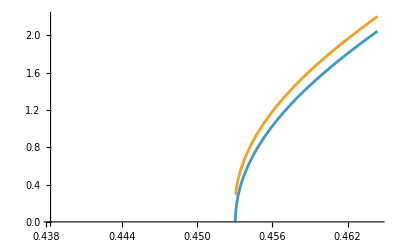

```mathematica
Plot[{10^7 dBrFree[s, "BKtautau",""],10^7 dΓBrCoulomb[s, "BKtautau",""]},{s, 3.87mhat[mtau,MB],  4.1mhat[mtau,MB]}]
```

```mathematica
dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s<=(Sqrt[8]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=1/2(dBrFree [(Sqrt[8]1000)^2/MB^2, decay, boundary]+dBrFree [(Sqrt[11]1000)^2/MB^2, decay, boundary])/;s>=(Sqrt[8]1000)^2/MB^2/;s<(Sqrt[11]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s>=(Sqrt[11]1000)^2/MB^2/;s<(Sqrt[12.5]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=1/2(dBrFree [(Sqrt[12.5]1000)^2/MB^2, decay, boundary]+dBrFree [(Sqrt[15]1000)^2/MB^2, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MB^2/;s<(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/;s>=(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]




dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s<=(Sqrt[8]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=1/2(dBrFree [(Sqrt[8]1000)^2/MBs^2, decay, boundary]+dBrFree [(Sqrt[11]1000)^2/MBs^2, decay, boundary])/;s>=(Sqrt[8]1000)^2/MBs^2/;s<(Sqrt[11]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s>=(Sqrt[11]1000)^2/MBs^2/;s<(Sqrt[12.5]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=1/2(dBrFree [(Sqrt[12.5]1000)^2/MBs^2, decay, boundary]+dBrFree [(Sqrt[15]1000)^2/MBs^2, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MBs^2/;s<(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/;s>=(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]


dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s<=0.46/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrFreeCons[s_, decay_, boundary_] :=1/2(dBrFree [0.46, decay, boundary]+dBrFree [0.5, decay, boundary])/;s>=0.46/;s<0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s>=0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]


dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s<=0.45/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrFreeCons[s_, decay_, boundary_] :=1/2(dBrFree [0.45, decay, boundary]+dBrFree [0.49, decay, boundary])/;s>=0.45/;s<0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrFreeCons[s_, decay_, boundary_] :=dBrFree [s, decay, boundary]/; s>=0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
```

```mathematica
dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s<=(Sqrt[8]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=1/2(dΓBrCoulomb [(Sqrt[8]1000)^2/MB^2, decay, boundary]+dΓBrCoulomb [(Sqrt[11]1000)^2/MB^2, decay, boundary])/;s>=(Sqrt[8]1000)^2/MB^2/;s<(Sqrt[11]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s>=(Sqrt[11]1000)^2/MB^2/;s<(Sqrt[12.5]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=1/2(dΓBrCoulomb [(Sqrt[12.5]1000)^2/MB^2, decay, boundary]+dΓBrCoulomb [(Sqrt[15]1000)^2/MB^2, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MB^2/;s<(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/;s>=(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]




dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s<=(Sqrt[8]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=1/2(dΓBrCoulomb [(Sqrt[8]1000)^2/MBs^2, decay, boundary]+dΓBrCoulomb [(Sqrt[11]1000)^2/MBs^2, decay, boundary])/;s>=(Sqrt[8]1000)^2/MBs^2/;s<(Sqrt[11]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s>=(Sqrt[11]1000)^2/MBs^2/;s<(Sqrt[12.5]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=1/2(dΓBrCoulomb [(Sqrt[12.5]1000)^2/MBs^2, decay, boundary]+dΓBrCoulomb [(Sqrt[15]1000)^2/MBs^2, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MBs^2/;s<(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/;s>=(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]


dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s<=0.46/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=1/2(dΓBrCoulomb [0.46, decay, boundary]+dΓBrCoulomb [0.5, decay, boundary])/;s>=0.46/;s<0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s>=0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]


dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s<=0.45/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=1/2(dΓBrCoulomb [0.45, decay, boundary]+dΓBrCoulomb [0.49, decay, boundary])/;s>=0.45/;s<0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrCoulombCons[s_, decay_, boundary_] :=dΓBrCoulomb [s, decay, boundary]/; s>=0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
```

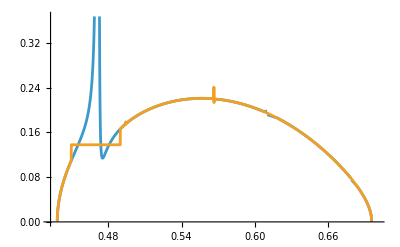

```mathematica
Plot[{10^7 dBrFree[x, "BsKtautau", ""],10^7 dBrFreeCons[x, "BsKtautau", ""]},{x, 3.95mhat[mtau,MBs],  0.7}]
```

```mathematica
dBrAngleFreeExtended[s_,cos_,type_,Mbmeson_, Mkaon_,Mlepton_, lep_,supp_, Γfulll_] := (Gfermi^2 Mbmeson^5 Abs[Vtd*Vtb]^2 α^2)/(Γfulll 512 Pi^5)(βV1[s,cos,type,Mbmeson, Mkaon,Mlepton, lep,supp]+ βV2[s,cos,type,Mbmeson, Mkaon,Mlepton, lep,supp]+4 mhat[Mlepton, Mbmeson] δV[s,type,Mbmeson, Mkaon,Mlepton])Sqrt[1/4 - mhat[Mlepton, Mbmeson]/s]Sqrt[ϕ[s,Mbmeson, Mkaon]]/; supp=="td"
dBrAngleFreeExtended[s_,cos_,type_,Mbmeson_, Mkaon_,Mlepton_, lep_,supp_, Γfulll_] := (Gfermi^2 Mbmeson^5 Abs[Vts*Vtb]^2 α^2)/(Γfulll 512 Pi^5)(βV1[s,cos,type,Mbmeson, Mkaon,Mlepton, lep,supp]+ βV2[s,cos,type,Mbmeson, Mkaon,Mlepton, lep,supp]+4 mhat[Mlepton, Mbmeson] δV[s,type,Mbmeson, Mkaon,Mlepton])Sqrt[1/4 - mhat[Mlepton, Mbmeson]/s]Sqrt[ϕ[s,Mbmeson, Mkaon]]/; supp=="ts"
```

```mathematica
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK",MB, Mk,me, "e","ts", Γfull]/; decay=="BKee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK+",MB, Mk,me, "e","ts", Γfull]/; decay=="BKee"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK-",MB, Mk,me, "e","ts", Γfull]/; decay=="BKee"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK",MB, Mk,mmu, "mu","ts", Γfull]/; decay=="BKmumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK+",MB, Mk,mmu, "mu","ts", Γfull]/; decay=="BKmumu"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK-",MB, Mk,mmu, "mu","ts", Γfull]/; decay=="BKmumu"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK",MB, Mk,mtau, "tau","ts", Γfull]/; decay=="BKtautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK+",MB, Mk,mtau, "tau","ts", Γfull]/; decay=="BKtautau"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BK-",MB, Mk,mtau, "tau","ts", Γfull]/; decay=="BKtautau"/; boundary == "-"



dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK",MBs, Mk,me, "e","td", ΓfullBs]/; decay=="BsKee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK+",MBs, Mk,me, "e","td", ΓfullBs]/; decay=="BsKee"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK-",MBs, Mk,me, "e","td", ΓfullBs]/; decay=="BsKee"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK",MBs, Mk,mmu, "mu","td", ΓfullBs]/; decay=="BsKmumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK+",MBs, Mk,mmu, "mu","td", ΓfullBs]/; decay=="BsKmumu"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK-",MBs, Mk,mmu, "mu","td", ΓfullBs]/; decay=="BsKmumu"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK",MBs, Mk,mtau, "tau","td", ΓfullBs]/; decay=="BsKtautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK+",MBs, Mk,mtau, "tau","td", ΓfullBs]/; decay=="BsKtautau"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"BsK-",MBs, Mk,mtau, "tau","td", ΓfullBs]/; decay=="BsKtautau"/; boundary == "-"



dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho",MB, Mrho,me, "e","ts", Γfull]/; decay=="Brhoee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho+",MB, Mrho,me, "e","ts", Γfull]/; decay=="Brhoee"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho-",MB, Mrho,me, "e","ts", Γfull]/; decay=="Brhoee"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho",MB, Mrho,mmu, "mu","ts", Γfull]/; decay=="Brhomumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho+",MB, Mrho,mmu, "mu","ts", Γfull]/; decay=="Brhomumu"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho-",MB, Mrho,mmu, "mu","ts", Γfull]/; decay=="Brhomumu"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho",MB, Mrho,mtau, "tau","ts", Γfull]/; decay=="Brhotautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho+",MB, Mrho,mtau, "tau","ts", Γfull]/; decay=="Brhotautau"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Brho-",MB, Mrho,mtau, "tau","ts", Γfull]/; decay=="Brhotautau"/; boundary == "-"


dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi",MBs, Mphi,me, "e","ts", ΓfullBs]/; decay=="Bsphiee"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi+",MBs, Mphi,me, "e","ts", ΓfullBs]/; decay=="Bsphiee"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi-",MBs, Mphi,me, "e","ts", ΓfullBs]/; decay=="Bsphiee"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi",MBs, Mphi,mmu, "mu","ts", ΓfullBs]/; decay=="Bsphimumu"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi+",MBs, Mphi,mmu, "mu","ts", ΓfullBs]/; decay=="Bsphimumu"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi-",MBs, Mphi,mmu, "mu","ts", ΓfullBs]/; decay=="Bsphimumu"/; boundary == "-"

dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi",MBs, Mphi,mtau, "tau","ts", ΓfullBs]/; decay=="Bsphitautau"/; boundary == ""
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi+",MBs, Mphi,mtau, "tau","ts", ΓfullBs]/; decay=="Bsphitautau"/; boundary == "+"
dBrAngleFree[s_,cos_, decay_, boundary_] := dBrAngleFreeExtended[s,cos,"Bsphi-",MBs, Mphi,mtau, "tau","ts", ΓfullBs]/; decay=="Bsphitautau"/; boundary == "-"
```

```mathematica
dBrAngleCoulomb [s_,cos_, decay_, boundary_] := dBrAngleFree [s,cos, decay, boundary]CAS[Vrel[mhat[Mlep[decay],Mbm[decay]]/s]]
```

```mathematica
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s<=(Sqrt[8]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree [(Sqrt[8]1000)^2/MB^2,cos, decay, boundary]+dBrAngleFree [(Sqrt[11]1000)^2/MB^2,cos, decay, boundary])/;s>=(Sqrt[8]1000)^2/MB^2/;s<(Sqrt[11]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s>=(Sqrt[11]1000)^2/MB^2/;s<(Sqrt[12.5]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree [(Sqrt[12.5]1000)^2/MB^2,cos, decay, boundary]+dBrAngleFree [(Sqrt[15]1000)^2/MB^2,cos, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MB^2/;s<(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/;s>=(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]




dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s<=(Sqrt[8]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree [(Sqrt[8]1000)^2/MBs^2,cos, decay, boundary]+dBrAngleFree [(Sqrt[11]1000)^2/MBs^2,cos, decay, boundary])/;s>=(Sqrt[8]1000)^2/MBs^2/;s<(Sqrt[11]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s>=(Sqrt[11]1000)^2/MBs^2/;s<(Sqrt[12.5]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree [(Sqrt[12.5]1000)^2/MBs^2,cos, decay, boundary]+dBrAngleFree [(Sqrt[15]1000)^2/MBs^2,cos, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MBs^2/;s<(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/;s>=(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]


dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s<=0.46/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree [0.46,cos, decay, boundary]+dBrAngleFree [0.5,cos, decay, boundary])/;s>=0.46/;s<0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s>=0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]


dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s<=0.45/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleFree [0.45,cos, decay, boundary]+dBrAngleFree [0.49,cos, decay, boundary])/;s>=0.45/;s<0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrAngleFreeCons[s_,cos_, decay_, boundary_] :=dBrAngleFree [s,cos, decay, boundary]/; s>=0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
```

```mathematica
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s<=(Sqrt[8]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleCoulomb [(Sqrt[8]1000)^2/MB^2,cos, decay, boundary]+dBrAngleCoulomb [(Sqrt[11]1000)^2/MB^2,cos, decay, boundary])/;s>=(Sqrt[8]1000)^2/MB^2/;s<(Sqrt[11]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s>=(Sqrt[11]1000)^2/MB^2/;s<(Sqrt[12.5]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleCoulomb [(Sqrt[12.5]1000)^2/MB^2,cos, decay, boundary]+dBrAngleCoulomb [(Sqrt[15]1000)^2/MB^2,cos, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MB^2/;s<(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/;s>=(Sqrt[15]1000)^2/MB^2/;MemberQ[{"BKee","BKmumu", "Brhoee", "Brhomumu"},decay]




dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s<=(Sqrt[8]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleCoulomb [(Sqrt[8]1000)^2/MBs^2,cos, decay, boundary]+dBrAngleCoulomb [(Sqrt[11]1000)^2/MBs^2,cos, decay, boundary])/;s>=(Sqrt[8]1000)^2/MBs^2/;s<(Sqrt[11]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s>=(Sqrt[11]1000)^2/MBs^2/;s<(Sqrt[12.5]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleCoulomb [(Sqrt[12.5]1000)^2/MBs^2,cos, decay, boundary]+dBrAngleCoulomb [(Sqrt[15]1000)^2/MBs^2,cos, decay, boundary])/;s>=(Sqrt[12.5]1000)^2/MBs^2/;s<(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/;s>=(Sqrt[15]1000)^2/MBs^2/;MemberQ[{"BsKee","BsKmumu", "Bsphiee", "Bsphimumu"},decay]


dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s<=0.46/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleCoulomb [0.46,cos, decay, boundary]+dBrAngleCoulomb [0.5,cos, decay, boundary])/;s>=0.46/;s<0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s>=0.5/;MemberQ[{"BKtautau", "Brhotautau"},decay]


dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s<=0.45/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=1/2(dBrAngleCoulomb [0.45,cos, decay, boundary]+dBrAngleCoulomb [0.49,cos, decay, boundary])/;s>=0.45/;s<0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
dBrAngleCoulombCons[s_,cos_, decay_, boundary_] :=dBrAngleCoulomb [s,cos, decay, boundary]/; s>=0.49/;MemberQ[{"BsKtautau", "Bsphitautau"},decay]
```

```mathematica
Plot3D[10^7 dBrAngleFree [s, cos, "BKmumu", ""], {s,4mhat[mmu, MB], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->10]
```

```mathematica
Plot[Quiet[10^7 NIntegrate[dBrAngleFreeCons [s, cos, "BKee", ""],{s,4mhat[me, MB], (1-Mk/MB)^2}]],{cos, -1, 1}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

### 3) Дифференциальная ширина, графики.

```mathematica
ClearAll[wthack]
wthack[clr_:Blue][{d___,h_HatchFilling}]:=PatternFilling[ColorReplace[Graphics[{d,h,Rectangle[]}],White->clr],ImageScaled[1]]
opac = 0.3;
clr = Black;
```

```mathematica
Plot[{10^7 dBrFree[x, "BKmumu","-"],10^7 1.02dΓBrCoulomb[x, "BKmumu","-"],10^7 dBrFree[x, "BKmumu","+"],10^7 1.02dΓBrCoulomb[x, "BKmumu","+"]}, {x, 4.1mhat[mmu,MB],  0.7},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
Plot[{10^7 dBrFree[x, "BKmumu","-"],10^7 1.02dΓBrCoulomb[x, "BKmumu","-"],10^7 dBrFree[x, "BKmumu","+"],10^7 1.02dΓBrCoulomb[x, "BKmumu","+"]}, {x, 4.05mhat[mmu,MB],  0.7},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
Plot[{10^7 dBrFree[x, "BsKtautau","-"],10^7 1.02dΓBrCoulomb[x, "BsKtautau","-"],10^7 dBrFree[x, "BsKtautau","+"],10^7 1.02dΓBrCoulomb[x, "BsKtautau","+"]}, {x, 3.95mhat[mtau,MBs],  0.7},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
PlotsBVll = {{Plot[{10^7 dBrFree[x, "BKee","-"],10^7 1.04dΓBrCoulomb[x, "BKee","-"],10^7 dBrFree[x, "BKee","+"],10^7 1.04dΓBrCoulomb[x, "BKee","+"]}, {x, 4mhat[me,MB], (1-Mk/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "BKmumu","-"],10^7 1.04dΓBrCoulomb[x, "BKmumu","-"],10^7 dBrFree[x, "BKmumu","+"],10^7 1.04dΓBrCoulomb[x, "BKee","+"]}, {x, 4.1mhat[mmu,MB], (1-Mk/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "BKtautau","-"],10^7 1.04dΓBrCoulomb[x, "BKtautau","-"],10^7 dBrFree[x, "BKtautau","+"],10^7 1.04dΓBrCoulomb[x, "BKtautau","+"]}, {x, 4mhat[mtau,MB], (1-Mk/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{10^7 dBrFree[x, "Brhoee","-"],10^7 1.04dΓBrCoulomb[x, "Brhoee","-"],10^7 dBrFree[x, "Brhoee","+"],10^7 1.04dΓBrCoulomb[x, "Brhoee","+"]}, {x, 4mhat[me,MB], (1-Mrho/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "Brhomumu","-"],10^7 1.04dΓBrCoulomb[x, "Brhomumu","-"],10^7 dBrFree[x, "Brhomumu","+"],10^7 1.04dΓBrCoulomb[x, "Brhomumu","+"]}, {x,  4.1mhat[mmu,MB], (1-Mrho/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "Brhotautau","-"],10^7 1.04dΓBrCoulomb[x, "Brhotautau","-"],10^7 dBrFree[x, "Brhotautau","+"],10^7 1.04dΓBrCoulomb[x, "Brhotautau","+"]}, {x,  4mhat[mtau,MB], (1-Mrho/MB)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{10^7 dBrFree[x, "Bsphiee","-"],10^7 1.04dΓBrCoulomb[x, "Bsphiee","-"],10^7 dBrFree[x, "Bsphiee","+"],10^7 1.04dΓBrCoulomb[x, "Bsphiee","+"]}, {x,  4mhat[me,MBs], (1-Mphi/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "Bsphimumu","-"],10^7 1.04dΓBrCoulomb[x, "Bsphimumu","-"],10^7 dBrFree[x, "Bsphimumu","+"],10^7 1.04dΓBrCoulomb[x, "Bsphimumu","+"]}, {x, 4.1mhat[mmu,MBs], (1-Mphi/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "Bsphitautau","-"],10^7 1.04dΓBrCoulomb[x, "Bsphitautau","-"],10^7 dBrFree[x, "Bsphitautau","+"],10^7 1.04dΓBrCoulomb[x, "Bsphitautau","+"]}, {x, 4mhat[mtau,MBs], (1-Mphi/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{10^7 dBrFree[x, "BsKee","-"],10^7 1.04dΓBrCoulomb[x, "BsKee","-"],10^7 dBrFree[x, "BsKee","+"],10^7 1.04dΓBrCoulomb[x, "BsKee","+"]}, {x, 4mhat[me,MBs], (1-Mk/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "BsKmumu","-"],10^7 1.04dΓBrCoulomb[x, "BsKmumu","-"],10^7 dBrFree[x, "BsKmumu","+"],10^7 1.04dΓBrCoulomb[x, "BsKee","+"]}, {x, 4.1mhat[mmu,MBs], (1-Mk/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1], Plot[{10^7 dBrFree[x, "BsKtautau","-"],10^7 1.04dΓBrCoulomb[x, "BsKtautau","-"],10^7 dBrFree[x, "BsKtautau","+"],10^7 1.04dΓBrCoulomb[x, "BsKtautau","+"]}, {x, 4mhat[mtau,MBs], (1-Mk/MBs)^2},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}}
```

```mathematica
TableForm[PlotsBVll]
```

```mathematica
Export["BVLLv5.pdf",TableForm[PlotsBVll],ImageResolution->500,"CompressionLevel"->0]
```

BVLLv5.pdf

```mathematica
Export["BVLL.pdf",TableForm[PlotsBVll]]
```

BVLL.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["BVLL.jpg"]]]
```

```mathematica
PlotsBVll3Dangle = {{Plot3D[10^6 dBrAngleCoulomb [s, cos, "BKee", ""], {s,4mhat[me, MB], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "BKmumu", ""], {s,4mhat[mmu, MB], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "BKtautau", ""], {s,4mhat[mtau, MB], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]},
{Plot3D[10^6 dBrAngleCoulomb [s, cos, "Brhoee", ""], {s,4mhat[me, MB], 0.8}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "Brhomumu", ""], {s,4mhat[mmu, MB], 0.8}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "Brhotautau", ""], {s,4mhat[mtau, MB], 0.75}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]},
{Plot3D[10^6 dBrAngleCoulomb [s, cos, "Bsphiee", ""], {s,4mhat[me, MBs], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "Bsphimumu", ""], {s,4mhat[mmu, MBs], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "Bsphitautau", ""], {s,4mhat[mtau, MBs], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]},
{Plot3D[10^6 dBrAngleCoulomb [s, cos, "BsKee", ""], {s,4mhat[me, MBs], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "BsKmumu", ""], {s,4mhat[mmu, MBs], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^6 dBrAngleCoulomb [s, cos, "BsKtautau", ""], {s,4mhat[mtau, MBs], 0.7}, {cos, -1, 1},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]}}
```

```mathematica
Export["BVLLangle3D.pdf",TableForm[PlotsBVll3Dangle],"CompressionLevel"->0]
```

BVLLangle3D.pdf

```mathematica
Export["BVLLangle3D.pdf",TableForm[PlotsBVll3Dangle],ImageResolution->2000,"CompressionLevel"->0]
```

BVLLangle3D.pdf

```mathematica
Integrate[1/Sqrt[1 - k Cos[x]], {x, 0, 2 Pi},Assumptions->k>0]
```

(2 EllipticK[(2 k)/(-1+k)])/(√(1-k))+(2 EllipticK[(2 k)/(1+k)])/(√(1+k))

```mathematica
EllipticK
```

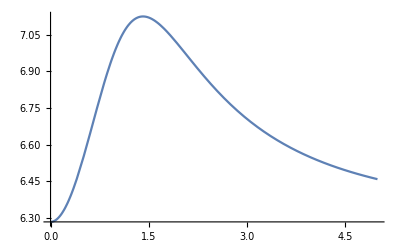

```mathematica
Plot[NIntegrate[1/Sqrt[1 - (2r)/(2 + r^2) Cos[x]], {x, 0, 2 Pi}], {r, 0, 5}]
```

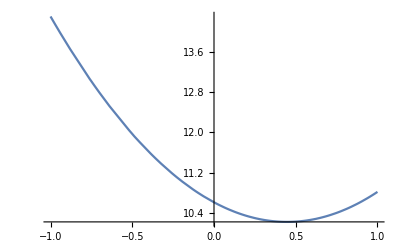

```mathematica
Plot[10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhoee", "+"],{s, 4mhat[me,MB], (1-Mrho/MB)^2}]], {cos, -1, 1},PlotPoints->5]
```

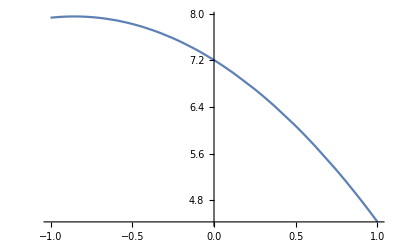

```mathematica
Plot[10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhoee", "+"],{s, 4mhat[mmu,MB], (1-Mrho/MB)^2}]], {cos, -1, 1},PlotPoints->5]
```

```mathematica
Export["BKeeangle1.pdf",-Graphics-,ImageResolution->2000,"CompressionLevel"->0]
```

BKeeangle1.pdf

```mathematica
PlotsAngleBKLL = {Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BKee", "-"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BKee", "-"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BKee", "+"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BKee", "+"],{s, 4mhat[me,MB], (1-Mk/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BKmumu", "-"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BKmumu", "-"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BKmumu", "+"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BKmumu", "+"],{s, 4mhat[mmu,MB], (1-Mk/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1] , Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BKtautau", "-"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BKtautau", "-"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BKtautau", "+"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BKtautau", "+"],{s, 4mhat[mtau,MB], (1-Mk/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}
```

```mathematica
PlotsAngleBrhoLL = {Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhoee", "-"],{s, 4mhat[me,MB], (1-Mrho/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Brhoee", "-"],{s, 4mhat[me,MB], (1-Mrho/MB)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhoee", "+"],{s, 4mhat[me,MB], (1-Mrho/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Brhoee", "+"],{s, 4mhat[me,MB], (1-Mrho/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhomumu", "-"],{s, 4mhat[mmu,MB], (1-Mrho/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Brhomumu", "-"],{s, 4mhat[mmu,MB], (1-Mrho/MB)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhomumu", "+"],{s, 4mhat[mmu,MB], (1-Mrho/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Brhomumu", "+"],{s, 4mhat[mmu,MB], (1-Mrho/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1] ,Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhotautau", "-"],{s, 4mhat[mtau,MB], (1-Mrho/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Brhotautau", "-"],{s, 4mhat[mtau,MB], (1-Mrho/MB)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Brhotautau", "+"],{s, 4mhat[mtau,MB], (1-Mrho/MB)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Brhotautau", "+"],{s, 4mhat[mtau,MB], (1-Mrho/MB)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1] }
```

```mathematica
PlotsAngleBsphiLL = {Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Bsphiee", "-"],{s, 4mhat[me,MBs], (1-Mphi/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Bsphiee", "-"],{s, 4mhat[me,MBs], (1-Mphi/MBs)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Bsphiee", "+"],{s, 4mhat[me,MBs], (1-Mphi/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Bsphiee", "+"],{s, 4mhat[me,MBs], (1-Mphi/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1] ,Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Bsphimumu", "-"],{s, 4mhat[mmu,MBs], (1-Mphi/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Bsphimumu", "-"],{s, 4mhat[mmu,MBs], (1-Mphi/MBs)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Bsphimumu", "+"],{s, 4mhat[mmu,MBs], (1-Mphi/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Bsphimumu", "+"],{s, 4mhat[mmu,MBs], (1-Mphi/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Bsphitautau", "-"],{s, 4mhat[mtau,MBs], (1-Mphi/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Bsphitautau", "-"],{s, 4mhat[mtau,MBs], (1-Mphi/MBs)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "Bsphitautau", "+"],{s, 4mhat[mtau,MBs], (1-Mphi/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "Bsphitautau", "+"],{s, 4mhat[mtau,MBs], (1-Mphi/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]  }
```

```mathematica
PlotsAngleBsKLL = {Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BsKee", "-"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BsKee", "-"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BsKee", "+"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BsKee", "+"],{s, 4mhat[me,MBs], (1-Mk/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BsKmumu", "-"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BsKmumu", "-"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BsKmumu", "+"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BsKmumu", "+"],{s, 4mhat[mmu,MBs], (1-Mk/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1] , Plot[{10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BsKtautau", "-"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BsKtautau", "-"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]], 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,cos, "BsKtautau", "+"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]],1.02 10^7 Quiet[NIntegrate[dBrAngleCoulombCons[s,cos, "BsKtautau", "+"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]]},{cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}
```

```mathematica
TableForm[{PlotsAngleBKLL, PlotsAngleBrhoLL,PlotsAngleBsphiLL, PlotsAngleBsKLL}]
```

```mathematica
Export["BVLLanglev5.pdf",TableForm[{PlotsAngleBKLL, PlotsAngleBrhoLL,PlotsAngleBsphiLL, PlotsAngleBsKLL}],ImageResolution->500,"CompressionLevel"->0]
```

BVLLanglev5.pdf

```mathematica
10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,0, "BsKtautau", "+"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]] - 10^7 Quiet[NIntegrate[dBrAngleFreeCons[s,0, "BsKtautau", "+"],{s, 4mhat[mtau,MBs], (1-Mk/MBs)^2}]]
```

0.0100261

```mathematica
0.010026080153220991/0.015
```

0.668405

### 4) Branching ratio, расчеты.

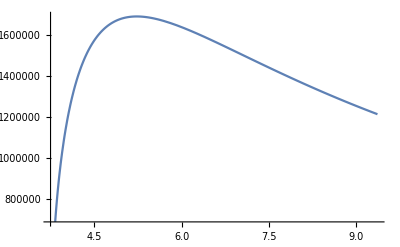

```mathematica
Plot[10^6 dBrFreeCons[x, "BKee", "-"], {x, 4mhat[me,MB], 10mhat[me,MB]}]
```

```mathematica
IntegralsBKee = {NIntegrate[dBrFreeCons[x, "BKee", "-"], {x, 4mhat[me,MB], (1-Mk/MB)^2}],NIntegrate[dBrFreeCons[x, "BKee", "+"], {x, 4mhat[me,MB], (1-Mk/MB)^2}],NIntegrate[dBrCoulombCons[x, "BKee", "-"], {x, 4mhat[me,MB],(1-Mk/MB)^2}],NIntegrate[dBrCoulombCons[x, "BKee", "+"], {x, 4mhat[me,MB],(1-Mk/MB)^2}]};
ΓfreeBKee = {(IntegralsBKee[[1]]+IntegralsBKee[[2]])/2, (IntegralsBKee[[2]]-IntegralsBKee[[1]])/4,(IntegralsBKee[[3]]+IntegralsBKee[[4]])/2, (IntegralsBKee[[4]]-IntegralsBKee[[3]])/4, 100(IntegralsBKee[[3]]-IntegralsBKee[[1]])/IntegralsBKee[[1]]};
IntegralsBKmumu = {NIntegrate[dBrFreeCons[x, "BKmumu", "-"], {x, 4mhat[mmu,MB], (1-Mk/MB)^2}],NIntegrate[dBrFreeCons[x, "BKmumu", "+"], {x, 4mhat[mmu,MB], (1-Mk/MB)^2}],NIntegrate[dBrCoulombCons[x, "BKmumu", "-"], {x, 4mhat[mmu,MB],(1-Mk/MB)^2}],NIntegrate[dBrCoulombCons[x, "BKmumu", "+"], {x, 4mhat[mmu,MB],(1-Mk/MB)^2}]};
ΓfreeBKmumu = {(IntegralsBKmumu[[1]]+IntegralsBKmumu[[2]])/2, (IntegralsBKmumu[[2]]-IntegralsBKmumu[[1]])/4,(IntegralsBKmumu[[3]]+IntegralsBKmumu[[4]])/2, (IntegralsBKmumu[[4]]-IntegralsBKmumu[[3]])/4, 100(IntegralsBKmumu[[3]]-IntegralsBKmumu[[1]])/IntegralsBKmumu[[1]]};
IntegralsBKtautau = {NIntegrate[dBrFreeCons[x, "BKtautau", "-"], {x, 4mhat[mtau,MB], (1-Mk/MB)^2}],NIntegrate[dBrFreeCons[x, "BKtautau", "+"], {x, 4mhat[mtau,MB], (1-Mk/MB)^2}],NIntegrate[dBrCoulombCons[x, "BKtautau", "-"], {x, 4mhat[mtau,MB],(1-Mk/MB)^2}],NIntegrate[dBrCoulombCons[x, "BKtautau", "+"], {x, 4mhat[mtau,MB],(1-Mk/MB)^2}]};
ΓfreeBKtautau = {(IntegralsBKtautau[[1]]+IntegralsBKtautau[[2]])/2, (IntegralsBKtautau[[2]]-IntegralsBKtautau[[1]])/4,(IntegralsBKtautau[[3]]+IntegralsBKtautau[[4]])/2, (IntegralsBKtautau[[4]]-IntegralsBKtautau[[3]])/4, 100(IntegralsBKtautau[[3]]-IntegralsBKtautau[[1]])/IntegralsBKtautau[[1]]}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.39528}. NIntegrate obtained 1.07798×10^-6 and 8.8672×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.449245}. NIntegrate obtained 1.65934×10^-6 and 1.40258×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.39528}. NIntegrate obtained 1.10315×10^-6 and 9.05626×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.53864}. NIntegrate obtained 7.74172×10^-7 and 4.10527×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.53864}. NIntegrate obtained 1.21501×10^-6 and 6.71777×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.53864}. NIntegrate obtained 7.92281×10^-7 and 4.20085×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.585362}. NIntegrate obtained 4.93304×10^-8 and 7.37762×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.585362}. NIntegrate obtained 8.41766×10^-8 and 1.39242×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.585362}. NIntegrate obtained 5.11508×10^-8 and 7.33879×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{6.67535×10^-8,8.71156×10^-9,6.91953×10^-8,9.02226×10^-9,3.6903}

```mathematica
{ΓfreeBKee,ΓfreeBKmumu,ΓfreeBKee[[1]]/ΓfreeBKmumu[[1]]}
```

{{1.36866×10^-6,1.4534×10^-7,1.40111×10^-6,1.48779×10^-7,2.3729},{9.94589×10^-7,1.10209×10^-7,1.01846×10^-6,1.12837×10^-7,2.40404},1.3761}

```mathematica
IntegralsBrhoee = {NIntegrate[dBrFreeCons[x, "Brhoee", "-"], {x, 4mhat[me,MB], (1-Mrho/MB)^2}],NIntegrate[dBrFreeCons[x, "Brhoee", "+"], {x, 4mhat[me,MB], (1-Mrho/MB)^2}],NIntegrate[dBrCoulombCons[x, "Brhoee", "-"], {x, 4mhat[me,MB],(1-Mrho/MB)^2}],NIntegrate[dBrCoulombCons[x, "Brhoee", "+"], {x, 4mhat[me,MB],(1-Mrho/MB)^2}]};
ΓfreeBrhoee = {(IntegralsBrhoee[[1]]+IntegralsBrhoee[[2]])/2, (IntegralsBrhoee[[2]]-IntegralsBrhoee[[1]])/4,(IntegralsBrhoee[[3]]+IntegralsBrhoee[[4]])/2, (IntegralsBrhoee[[4]]-IntegralsBrhoee[[3]])/4, 100(IntegralsBrhoee[[3]]-IntegralsBrhoee[[1]])/IntegralsBrhoee[[1]]};
IntegralsBrhomumu = {NIntegrate[dBrFreeCons[x, "Brhomumu", "-"], {x, 4mhat[mmu,MB], (1-Mrho/MB)^2}],NIntegrate[dBrFreeCons[x, "Brhomumu", "+"], {x, 4mhat[mmu,MB], (1-Mrho/MB)^2}],NIntegrate[dBrCoulombCons[x, "Brhomumu", "-"], {x, 4mhat[mmu,MB],(1-Mrho/MB)^2}],NIntegrate[dBrCoulombCons[x, "Brhomumu", "+"], {x, 4mhat[mmu,MB],(1-Mrho/MB)^2}]};
ΓfreeBrhomumu = {(IntegralsBrhomumu[[1]]+IntegralsBrhomumu[[2]])/2, (IntegralsBrhomumu[[2]]-IntegralsBrhomumu[[1]])/4,(IntegralsBrhomumu[[3]]+IntegralsBrhomumu[[4]])/2, (IntegralsBrhomumu[[4]]-IntegralsBrhomumu[[3]])/4, 100(IntegralsBrhomumu[[3]]-IntegralsBrhomumu[[1]])/IntegralsBrhomumu[[1]]};
IntegralsBrhotautau = {NIntegrate[dBrFreeCons[x, "Brhotautau", "-"], {x, 4mhat[mtau,MB], (1-Mrho/MB)^2}],NIntegrate[dBrFreeCons[x, "Brhotautau", "+"], {x, 4mhat[mtau,MB], (1-Mrho/MB)^2}],NIntegrate[dBrCoulombCons[x, "Brhotautau", "-"], {x, 4mhat[mtau,MB],(1-Mrho/MB)^2}],NIntegrate[dBrCoulombCons[x, "Brhotautau", "+"], {x, 4mhat[mtau,MB],(1-Mrho/MB)^2}]};
ΓfreeBrhotautau = {(IntegralsBrhotautau[[1]]+IntegralsBrhotautau[[2]])/2, (IntegralsBrhotautau[[2]]-IntegralsBrhotautau[[1]])/4,(IntegralsBrhotautau[[3]]+IntegralsBrhotautau[[4]])/2, (IntegralsBrhotautau[[4]]-IntegralsBrhotautau[[3]])/4, 100(IntegralsBrhotautau[[3]]-IntegralsBrhotautau[[1]])/IntegralsBrhotautau[[1]]};




IntegralsBsKee = {NIntegrate[dBrFreeCons[x, "BsKee", "-"], {x, 4mhat[me,MBs], (1-Mk/MBs)^2}],NIntegrate[dBrFreeCons[x, "BsKee", "+"], {x, 4mhat[me,MBs], (1-Mk/MBs)^2}],NIntegrate[dBrCoulombCons[x, "BsKee", "-"], {x, 4mhat[me,MBs],(1-Mk/MBs)^2}],NIntegrate[dBrCoulombCons[x, "BsKee", "+"], {x, 4mhat[me,MBs],(1-Mk/MBs)^2}]};
ΓfreeBsKee = {(IntegralsBsKee[[1]]+IntegralsBsKee[[2]])/2, (IntegralsBsKee[[2]]-IntegralsBsKee[[1]])/4,(IntegralsBsKee[[3]]+IntegralsBsKee[[4]])/2, (IntegralsBsKee[[4]]-IntegralsBsKee[[3]])/4, 100(IntegralsBsKee[[3]]-IntegralsBsKee[[1]])/IntegralsBsKee[[1]]};
IntegralsBsKmumu = {NIntegrate[dBrFreeCons[x, "BsKmumu", "-"], {x, 4mhat[mmu,MBs], (1-Mk/MBs)^2}],NIntegrate[dBrFreeCons[x, "BsKmumu", "+"], {x, 4mhat[mmu,MBs], (1-Mk/MBs)^2}],NIntegrate[dBrCoulombCons[x, "BsKmumu", "-"], {x, 4mhat[mmu,MBs],(1-Mk/MBs)^2}],NIntegrate[dBrCoulombCons[x, "BsKmumu", "+"], {x, 4mhat[mmu,MBs],(1-Mk/MBs)^2}]};
ΓfreeBsKmumu = {(IntegralsBsKmumu[[1]]+IntegralsBsKmumu[[2]])/2, (IntegralsBsKmumu[[2]]-IntegralsBsKmumu[[1]])/4,(IntegralsBsKmumu[[3]]+IntegralsBsKmumu[[4]])/2, (IntegralsBsKmumu[[4]]-IntegralsBsKmumu[[3]])/4, 100(IntegralsBsKmumu[[3]]-IntegralsBsKmumu[[1]])/IntegralsBsKmumu[[1]]};
IntegralsBsKtautau = {NIntegrate[dBrFreeCons[x, "BsKtautau", "-"], {x, 4mhat[mtau,MBs], (1-Mk/MBs)^2}],NIntegrate[dBrFreeCons[x, "BsKtautau", "+"], {x, 4mhat[mtau,MBs], (1-Mk/MBs)^2}],NIntegrate[dBrCoulombCons[x, "BsKtautau", "-"], {x, 4mhat[mtau,MBs],(1-Mk/MBs)^2}],NIntegrate[dBrCoulombCons[x, "BsKtautau", "+"], {x, 4mhat[mtau,MBs],(1-Mk/MBs)^2}]};
ΓfreeBsKtautau = {(IntegralsBsKtautau[[1]]+IntegralsBsKtautau[[2]])/2, (IntegralsBsKtautau[[2]]-IntegralsBsKtautau[[1]])/4,(IntegralsBsKtautau[[3]]+IntegralsBsKtautau[[4]])/2, (IntegralsBsKtautau[[4]]-IntegralsBsKtautau[[3]])/4, 100(IntegralsBsKtautau[[3]]-IntegralsBsKtautau[[1]])/IntegralsBsKtautau[[1]]}; 





IntegralsBsphiee = {NIntegrate[dBrFreeCons[x, "Bsphiee", "-"], {x, 4mhat[me,MBs], (1-Mphi/MBs)^2}],NIntegrate[dBrFreeCons[x, "Bsphiee", "+"], {x, 4mhat[me,MBs], (1-Mphi/MBs)^2}],NIntegrate[dBrCoulombCons[x, "Bsphiee", "-"], {x, 4mhat[me,MBs],(1-Mphi/MBs)^2}],NIntegrate[dBrCoulombCons[x, "Bsphiee", "+"], {x, 4mhat[me,MBs],(1-Mphi/MBs)^2}]};
ΓfreeBsphiee = {(IntegralsBsphiee[[1]]+IntegralsBsphiee[[2]])/2, (IntegralsBsphiee[[2]]-IntegralsBsphiee[[1]])/4,(IntegralsBsphiee[[3]]+IntegralsBsphiee[[4]])/2, (IntegralsBsphiee[[4]]-IntegralsBsphiee[[3]])/4, 100(IntegralsBsphiee[[3]]-IntegralsBsphiee[[1]])/IntegralsBsphiee[[1]]};
IntegralsBsphimumu = {NIntegrate[dBrFreeCons[x, "Bsphimumu", "-"], {x, 4mhat[mmu,MBs], (1-Mphi/MBs)^2}],NIntegrate[dBrFreeCons[x, "Bsphimumu", "+"], {x, 4mhat[mmu,MBs], (1-Mphi/MBs)^2}],NIntegrate[dBrCoulombCons[x, "Bsphimumu", "-"], {x, 4mhat[mmu,MBs],(1-Mphi/MBs)^2}],NIntegrate[dBrCoulombCons[x, "Bsphimumu", "+"], {x, 4mhat[mmu,MBs],(1-Mphi/MBs)^2}]};
ΓfreeBsphimumu = {(IntegralsBsphimumu[[1]]+IntegralsBsphimumu[[2]])/2, (IntegralsBsphimumu[[2]]-IntegralsBsphimumu[[1]])/4,(IntegralsBsphimumu[[3]]+IntegralsBsphimumu[[4]])/2, (IntegralsBsphimumu[[4]]-IntegralsBsphimumu[[3]])/4, 100(IntegralsBsphimumu[[3]]-IntegralsBsphimumu[[1]])/IntegralsBsphimumu[[1]]};
IntegralsBsphitautau = {NIntegrate[dBrFreeCons[x, "Bsphitautau", "-"], {x, 4mhat[mtau,MBs], (1-Mphi/MBs)^2}],NIntegrate[dBrFreeCons[x, "Bsphitautau", "+"], {x, 4mhat[mtau,MBs], (1-Mphi/MBs)^2}],NIntegrate[dBrCoulombCons[x, "Bsphitautau", "-"], {x, 4mhat[mtau,MBs],(1-Mphi/MBs)^2}],NIntegrate[dBrCoulombCons[x, "Bsphitautau", "+"], {x, 4mhat[mtau,MBs],(1-Mphi/MBs)^2}]};
ΓfreeBsphitautau = {(IntegralsBsphitautau[[1]]+IntegralsBsphitautau[[2]])/2, (IntegralsBsphitautau[[2]]-IntegralsBsphitautau[[1]])/4,(IntegralsBsphitautau[[3]]+IntegralsBsphitautau[[4]])/2, (IntegralsBsphitautau[[4]]-IntegralsBsphitautau[[3]])/4, 100(IntegralsBsphitautau[[3]]-IntegralsBsphitautau[[1]])/IntegralsBsphitautau[[1]]}; 

Γall = {{ΓfreeBKee, ΓfreeBKmumu, ΓfreeBKtautau}, {ΓfreeBrhoee, ΓfreeBrhomumu, ΓfreeBrhotautau}, {ΓfreeBsphiee,ΓfreeBsphimumu, ΓfreeBsphitautau}, {ΓfreeBsKee, ΓfreeBsKmumu, ΓfreeBsKtautau}};

MatrixForm[Γall]
```

((1.36866×10^-6
1.4534×10^-7
1.40061×10^-6
1.48732×10^-7
2.3349) | (9.94589×10^-7
1.10209×10^-7
1.01785×10^-6
1.12783×10^-7
2.33921) | (6.67535×10^-8
8.71156×10^-9
6.91953×10^-8
9.02226×10^-9
3.6903)
(1.75703×10^-6
2.4789×10^-7
1.79814×10^-6
2.53682×10^-7
2.34125) | (1.01062×10^-6
1.66139×10^-7
1.03437×10^-6
1.70029×10^-7
2.35492) | (1.05873×10^-7
1.93983×10^-8
1.09453×10^-7
2.00395×10^-8
3.42527)
(2.87815×10^-6
2.46353×10^-7
2.94558×10^-6
2.52114×10^-7
2.34361) | (1.42018×10^-6
1.50269×10^-7
1.45371×10^-6
1.53795×10^-7
2.36414) | (8.11608×10^-8
1.03999×10^-8
8.41697×10^-8
1.07724×10^-8
3.75048)
(9.6882×10^-8
9.32051×10^-9
9.91502×10^-8
9.53844×10^-9
2.34195) | (5.2153×10^-8
5.83352×10^-9
5.3381×10^-8
5.97034×10^-9
2.35749) | (4.3018×10^-9
5.04198×10^-10
4.45295×10^-9
5.2138×10^-10
3.54608))

### 5) Ответ.

```mathematica
TableForm[PlotsBVll]
```

```mathematica
MatrixForm[Γall]
```

((1.65293×10^-6
1.55118×10^-7
1.69202×10^-6
1.58766×10^-7
2.36725) | (1.27411×10^-6
1.3014×10^-7
1.3045×10^-6
1.33216×10^-7
2.39093) | (1.19602×10^-7
1.18532×10^-8
1.27223×10^-7
1.25858×10^-8
6.41941)
(1.07726×10^-6
1.82769×10^-7
1.10263×10^-6
1.87054×10^-7
2.36067) | (8.87501×10^-7
1.61342×10^-7
9.08526×10^-7
1.65138×10^-7
2.37833) | (1.30635×10^-7
2.31963×10^-8
1.3814×10^-7
2.45×10^-8
5.81284)
(1.52129×10^-6
1.67123×10^-7
1.55729×10^-6
1.71051×10^-7
2.37137) | (1.15358×10^-6
1.42112×10^-7
1.18113×10^-6
1.45467×10^-7
2.3973) | (1.04693×10^-7
1.28847×10^-8
1.11527×10^-7
1.36974×10^-8
6.59878)
(5.56016×10^-8
6.50131×10^-9
5.69138×10^-8
6.65398×10^-9
2.36358) | (4.42438×10^-8
5.58576×10^-9
4.5296×10^-8
5.71754×10^-9
2.38481) | (5.32855×10^-9
6.1812×10^-10
5.65123×10^-9
6.54467×10^-10
6.10851))

$Aborted